# LLP decays

## Kinematics

## Lorentz boosts

```mathematica
SetDirectory[NotebookDirectory[]];
(*Position of the point in coordinate space in terms of spherical coordinates*)
ϕVal[px_,py_]=If[py>0,ArcCos[px/(√(px^2+py^2))],-ArcCos[px/(√(px^2+py^2))]];
θVal[px_,py_,pz_]=ArcCos[pz/(√(px^2+py^2+pz^2))];
(*Decaying particle momentum and velocity at its lab frame. Since the experiment geometry is convenient to characterize in terms of spherical coordinates, it is given here in both spherical and cartesian coordinates*)
pMotherVecCart[px_,py_,pz_]={px,py,pz};
vMotherVecCart[Ev_,px_,py_,pz_]=+pMotherVecCart[px,py,pz]/Ev;
(*γ,Γ factors*)
γFactor[ELLP_,mLLP_]=ELLP/mLLP;
Γfactor[ELLP_,mLLP_]=Simplify[(γFactor[ELLP,mLLP]-1)/(((v/.Solve[γFactor[ELLP,mLLP]==1/(√(1-v^2)),v])^2)[[1]])];
pprod={pxd,pyd,pzd};
vmotherlab=vMotherVecCart[Em,pxm,pym,pzm];
pproductLabVecCart[pxm_,pym_,pzm_,Em_,mm_,pxd_,pyd_,pzd_,Ed_]=Simplify[pprod+γFactor[Em,mm]*vmotherlab*Ed+Γfactor[Em,mm]*vmotherlab(vmotherlab.pprod)];
EproductLabCart[pxm_,pym_,pzm_,Em_,mm_,pxd_,pyd_,pzd_,Ed_]=Simplify[γFactor[Em,mm](Ed+vmotherlab.pprod)];
{pproductLab1Cart[pxm_,pym_,pzm_,Em_,mm_,pxd_,pyd_,pzd_,Ed_],pproductLab2Cart[pxm_,pym_,pzm_,Em_,mm_,pxd_,pyd_,pzd_,Ed_],pproductLab3Cart[pxm_,pym_,pzm_,Em_,mm_,pxd_,pyd_,pzd_,Ed_]}=Simplify[pproductLabVecCart[pxm,pym,pzm,Em,mm,pxd,pyd,pzd,Ed][[#]]]&/@{1,2,3};
Print["Check that (E^2)_boosted - ((p̄)^2)_boosted = m^2:"]
testExpr[pxm_,pym_,pzm_,Em_,mm_,pxd_,pyd_,pzd_,Ed_]=((EproductLabCart[pxm,pym,pzm,Em,mm,pxd,pyd,pzd,Ed]^2-pproductLab1Cart[pxm,pym,pzm,Em,mm,pxd,pyd,pzd,Ed]^2-pproductLab2Cart[pxm,pym,pzm,Em,mm,pxd,pyd,pzd,Ed]^2-pproductLab3Cart[pxm,pym,pzm,Em,mm,pxd,pyd,pzd,Ed]^2//Expand//Simplify)/.{pxm^2->Em^2-pym^2-pzm^2-mm^2}//Expand//Simplify)/.{Em^2->pxm^2+pym^2+pzm^2+mm^2};
testExpr[pxm,pym,pzm,√(pxm^2+pym^2+pzm^2+mm^2),mm,√(Ed^2-pyd^2-pzd^2-m^2),pyd,pzd,Ed]//Simplify
(*The same but assuming that the mother 3-momentum is given in terms of spherical coordinates*)
pMotherVecSpher[ELLP_,mLLP_,θLLP_,ϕLLP_]=√(ELLP^2-mLLP^2){Sin[θLLP]*Cos[ϕLLP],Sin[θLLP]*Sin[ϕLLP],Cos[θLLP]};
vMotherVecSpher[ELLP_,mLLP_,θLLP_,ϕLLP_]=+(pMotherVecSpher[ELLP,mLLP,θLLP,ϕLLP]/ELLP);
pproductLabVecSpher[ELLP_,mLLP_,θLLP_,ϕLLP_,pxd_,pyd_,pzd_,Ed_]=Simplify[pprod+γFactor[ELLP,mLLP]*vMotherVecSpher[ELLP,mLLP,θLLP,ϕLLP]*Ed+Γfactor[ELLP,mLLP]*vMotherVecSpher[ELLP,mLLP,θLLP,ϕLLP](vMotherVecSpher[ELLP,mLLP,θLLP,ϕLLP].pprod)];
EproductLabSpher[ELLP_,mLLP_,θLLP_,ϕLLP_,pxd_,pyd_,pzd_,Ed_]=Simplify[γFactor[ELLP,mLLP](Ed+vMotherVecSpher[ELLP,mLLP,θLLP,ϕLLP].pprod)];
{pproductLab1Spher[ELLP_,mLLP_,θLLP_,ϕLLP_,pxd_,pyd_,pzd_,Ed_],pproductLab2Spher[ELLP_,mLLP_,θLLP_,ϕLLP_,pxd_,pyd_,pzd_,Ed_],pproductLab3Spher[ELLP_,mLLP_,θLLP_,ϕLLP_,pxd_,pyd_,pzd_,Ed_]}=Simplify[pproductLabVecSpher[ELLP,mLLP,θLLP,ϕLLP,pxd,pyd,pzd,Ed][[#]]&/@{1,2,3}];
Print["Check that (E^2)_boosted - ((p̄)^2)_boosted = m^2 - for the formulas expressed in spherical LLP coordinates:"]
testExpr2[ELLP_,mLLP_,θLLP_,ϕLLP_,pxd_,pyd_,pzd_,Ed_]=EproductLabSpher[ELLP,mLLP,θLLP,ϕLLP,pxd,pyd,pzd,Ed]^2-pproductLab1Spher[ELLP,mLLP,θLLP,ϕLLP,pxd,pyd,pzd,Ed]^2-pproductLab2Spher[ELLP,mLLP,θLLP,ϕLLP,pxd,pyd,pzd,Ed]^2-pproductLab3Spher[ELLP,mLLP,θLLP,ϕLLP,pxd,pyd,pzd,Ed]^2//Expand//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Check that (E^2)_boosted - ((p̄)^2)_boosted = m^2:

m^2

Check that (E^2)_boosted - ((p̄)^2)_boosted = m^2 - for the formulas expressed in spherical LLP coordinates:

Ed^2-pxd^2-pyd^2-pzd^2

## Kinematics of 3-body decays

### Phase space in terms of energies E_1,E_3

```mathematica
(*Kinematics of 3-body decays*)
pPar[En_,mn_]=√(En^2-mn^2);
E2valEnergies[m_,E1_,E3_]=m-E1-E3;
(*cos between particles 1,2 and 1,3 at rest frame of decaying particle 0 -> 1+2+3 parametrized in terms of Subscript[E, 1],Subscript[E, 3]*)

cosθ12[E1_,E3_,m_,m1_,m2_,m3_]=(pPar[E3,m3]^2-pPar[E1,m1]^2-pPar[E2valEnergies[m,E1,E3],m2]^2)/(2pPar[E1,m1]*pPar[E2valEnergies[m,E1,E3],m2]);
cosθ13[E1_,E3_,m_,m1_,m2_,m3_]=(pPar[E2valEnergies[m,E1,E3],m2]^2-pPar[E1,m1]^2-pPar[E3,m3]^2)/(2pPar[E1,m1]*pPar[E3,m3]);
θ12[E1_,E3_,m_,m1_,m2_,m3_]=ArcCos[cosθ12[E1,E3,m,m1,m2,m3]];
θ13[E1_,E3_,m_,m1_,m2_,m3_]=ArcCos[cosθ13[E1,E3,m,m1,m2,m3]];
(*Domain of definition of Subscript[E, 1] and Subscript[E, 3] in decay 0->1+2+3 at rest frame of 0, Subscript[E, 3,min/max] = f(Subscript[E, 1])*)
E3domain[E1_,m_,m1_,m2_,m3_]=E3/.(*Assuming[m>0&&E1>m1>0,*)Simplify[Solve[cosθ12[E1,E3,m,m1,m2,m3]==1,E3]](*]*)
E3domainMin[E1_,m_,m1_,m2_,m3_]=E3domain[E1,m,m1,m2,m3][[1]];
E3domainMax[E1_,m_,m1_,m2_,m3_]=E3domain[E1,m,m1,m2,m3][[2]];
ΔE3[E1_,m_,m1_,m2_,m3_]=E3domainMax[E1,m,m1,m2,m3]-E3domainMin[E1,m,m1,m2,m3]//Simplify
{E1domainMin[m_,m1_,m2_,m3_],E1domainMax[m_,m1_,m2_,m3_]}=E1domain[m_,m1_,m2_,m3_]={E1/.Solve[ΔE3[E1,m,m1,m2,m3][[2]]==0,E1][[2]],E1/.Solve[ΔE3[E1,m,m1,m2,m3][[2]]==0,E1][[3]]}//Simplify
(*Domain of definition of Subscript[E, 1] and Subscript[E, 3] in decay 0->1+2+3 at rest frame of 0, now Subscript[E, 1,min/max] = f(Subscript[E, 3])*)
E1domain1[E1_,m_,m1_,m2_,m3_]=E1/.(*Assuming[m>0&&E1>m1>0,*)Simplify[Solve[cosθ12[E1,E3,m,m1,m2,m3]==1,E1]](*]*);
E1domain1Min[E1_,m_,m1_,m2_,m3_]=E1domain1[E3,m,m1,m2,m3][[1]];
E1domain1Max[E1_,m_,m1_,m2_,m3_]=E1domain1[E3,m,m1,m2,m3][[2]];
ΔE1[E3_,m_,m1_,m2_,m3_]=E1domain1Max[E3,m,m1,m2,m3]-E1domain1Min[E3,m,m1,m2,m3]//Simplify;
{E3domain1Min[m_,m1_,m2_,m3_],E3domain1Max[m_,m1_,m2_,m3_]}=E3domain1[m_,m1_,m2_,m3_]={E3/.Solve[ΔE1[E3,m,m1,m2,m3][[2]]==0,E3][[2]],E3/.Solve[ΔE1[E3,m,m1,m2,m3][[2]]==0,E3][[3]]}//Simplify;
(*Mandelstam invariants in terms of energies*)
M13[E1_,E3_]=(E1+E3)^2-(pPar[E1,m1]^2+pPar[E3,m3]^2+2*pPar[E1,m1]*pPar[E3,m3]*cosθ13[E1,E3,m,m1,m2,m3])//Expand//Simplify
M12[E1_,E3_]=(E1+E2valEnergies[m,E1,E3])^2-(pPar[E1,m1]^2+pPar[E2valEnergies[m,E1,E3],m2]^2+2*pPar[E1,m1]*pPar[E2valEnergies[m,E1,E3],m2]*cosθ12[E1,E3,m,m1,m2,m3])//Expand//Simplify
Q2[E1_,E3_,m_,m2_]=(m^2+m2^2-2*m*E2valEnergies[m,E1,E3]);
(*Domain of the parameter space E1,E3 for Subscript[E, 1] ranging between Subscript[E, min],Subscript[E, max]*)
E12E23domain[m_,m1_,m2_,m3_,Emin_,Emax_]:=NIntegrate[UnitStep[E3v-Emin]*UnitStep[Emax-E3v],{E1v,E1domain[m,m1,m2,m3][[1]],E1domain[m,m1,m2,m3][[2]]},{E3v,Max[E3domain[E1v,m,m1,m2,m3][[1]],Emin],Min[Emax,E3domain[E1v,m,m1,m2,m3][[2]]]},Method->"AdaptiveMonteCarlo"]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{1/(4 E1 m-2 (m^2+m1^2))(√((E1^2-m1^2) (4 E1^2 m^2-4 E1 m (m^2+m1^2-m2^2-m3^2)+m^4+2 m^2 (m1^2-m2^2-m3^2)+m1^4-2 m1^2 m2^2-2 m1^2 m3^2+m2^4-2 m2^2 m3^2+m3^4))-2 E1^2 m+3 E1 m^2+E1 m1^2-E1 m2^2+E1 m3^2-m^3-m m1^2+m m2^2-m m3^2),-1/(4 E1 m-2 (m^2+m1^2))(√((E1^2-m1^2) (4 E1^2 m^2-4 E1 m (m^2+m1^2-m2^2-m3^2)+m^4+2 m^2 (m1^2-m2^2-m3^2)+m1^4-2 m1^2 m2^2-2 m1^2 m3^2+m2^4-2 m2^2 m3^2+m3^4))+2 E1^2 m-3 E1 m^2-E1 m1^2+E1 m2^2-E1 m3^2+m^3+m m1^2-m m2^2+m m3^2)}

(√((E1^2-m1^2) (4 E1^2 m^2-4 E1 m (m^2+m1^2-m2^2-m3^2)+m^4+2 m^2 (m1^2-m2^2-m3^2)+m1^4-2 m1^2 m2^2-2 m1^2 m3^2+m2^4-2 m2^2 m3^2+m3^4)))/(-2 E1 m+m^2+m1^2)

{m1,(m^2+m1^2-(m2+m3)^2)/(2 m)}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

2 E1 m+2 E3 m-m^2+m2^2

-2 E3 m+m^2+m3^2

#### Scalar products in terms of energies 1,3

```mathematica
ProductKK=m^2;
ProductK2K2=m2^2;
ProductK3K3=m3^2;
ProductK1K1=m1^2;
ProductKK2energy=m*E2valEnergies[m,E1,E3];
ProductKK1energy=m*E1;
ProductKK3energy=m*E3;
ProductK1K3energy=(M13[E1,E3]-m1^2-m3^2)/2;
ProductK1K2energy=(M12[E1,E3]-m1^2-m2^2)/2;
ProductK2K3energy=(m^2+m1^2-2*m*E1-m2^2-m3^2)/2;
```

#### Scalar products in terms of Mandelstam variables

```mathematica
ProductKK1mandelstam=(m^2+m1^2-m23)/2;
ProductKK3mandelstam=(m^2+m3^2-m12)/2;
ProductKK2mandelstam=(m^2-ProductKK1mandelstam-ProductKK3mandelstam)//Simplify;
ProductK1K2mandelstam=(m12-m1^2-m2^2)/2;
ProductK2K3mandelstam=(m23-m2^2-m3^2)/2;
ProductK1K3mandelstam=(m^2-2ProductKK2mandelstam+m2^2-m1^2-m3^2)/2//Simplify;
ScalarProduct3body[1,2]=ProductK1K2mandelstam;
ScalarProduct3body[2,3]=ProductK2K3mandelstam;
ScalarProduct3body[1,3]=ProductK1K3mandelstam;
ScalarProduct3body[1,1]=m1^2;
ScalarProduct3body[2,2]=m2^2;
ScalarProduct3body[3,3]=m3^2;
ProductKK-ProductK1K1-ProductK2K2-ProductK3K3-2*(ProductK1K2mandelstam+ProductK2K3mandelstam+ProductK1K3mandelstam)//Simplify
```

0

#### 4-momenta of decay products at rest frame as a function of energies E_1,E_3

```mathematica
(*Rotation matrices with around z axis (ϕ angle) and x axis (θ angle)*)
ϕRotMatrix[ϕ_]={{Cos[ϕ],Sin[ϕ],0},{-Sin[ϕ],Cos[ϕ],0},{0,0,1}};
θRotMatrix[θ_]={{1,0,0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}};
pvecUnrotated[px_,py_,pz_]={px,py,pz};
pvecRotated[px_,py_,pz_,θV_,ϕV_]=ϕRotMatrix[ϕV].θRotMatrix[θV].pvecUnrotated[px,py,pz];
(*Momenta at frame where Subscript[p, 1] is aligned along z axis*)
p1unrotated={0,0,pPar[E1,m1]};
p2unrotated={pPar[E2valEnergies[m,E1,E3],m2]*Sin[θ12[E1,E3,m,m1,m2,m3]]*Sin[κ],pPar[E2valEnergies[m,E1,E3],m2]*Sin[θ12[E1,E3,m,m1,m2,m3]]*Cos[κ],pPar[E2valEnergies[m,E1,E3],m2]*Cos[θ12[E1,E3,m,m1,m2,m3]]};
p3unrotated={-pPar[E3,m3]*Sin[θ13[E1,E3,m,m1,m2,m3]]*Sin[κ],-pPar[E3,m3]*Sin[θ13[E1,E3,m,m1,m2,m3]]*Cos[κ],pPar[E3,m3]*Cos[θ13[E1,E3,m,m1,m2,m3]]};
(*θrand=RandomReal[{0,Pi}];
ϕrand=RandomReal[{-Pi,Pi}];*)
p1rotated[E1_,m1_,θV_,ϕV_]=(*ϕRotMatrix[ϕV].θRotMatrix[θV].p1Unrotated*)pvecRotated[p1unrotated[[1]],p1unrotated[[2]],p1unrotated[[3]],θV,ϕV];
p1rotatedX[E1_,m1_,θV_,ϕV_]=p1rotated[E1,m1,θV,ϕV][[1]];
p1rotatedY[E1_,m1_,θV_,ϕV_]=p1rotated[E1,m1,θV,ϕV][[2]];
p1rotatedZ[E1_,m1_,θV_,ϕV_]=p1rotated[E1,m1,θV,ϕV][[3]];
p2rotated[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=pvecRotated[p2unrotated[[1]],p2unrotated[[2]],p2unrotated[[3]],θV,ϕV]//Simplify;
p2rotatedX[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p2rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[1]];
p2rotatedY[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p2rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[2]];
p2rotatedZ[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p2rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[3]];
p3rotated[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=pvecRotated[p3unrotated[[1]],p3unrotated[[2]],p3unrotated[[3]],θV,ϕV]//Simplify;
p3rotatedX[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p3rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[1]];
p3rotatedY[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p3rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[2]];
p3rotatedZ[E1_,E3_,m_,m1_,m2_,m3_,θV_,ϕV_,κ_]=p3rotated[E1,E3,m,m1,m2,m3,θV,ϕV,κ][[3]];
```

## Decays of various LLPs: processes, branching ratios, matrix elements

## Definitions

```mathematica
procList[LLP_]:=Select[Keys[DownValues@ListBrRatiosTemp][[All,1,#]]&/@{1,3}//Transpose,#[[1]]==LLP&][[All,2]]
procListnoecal[LLP_]:=Block[{},
prl=procList[LLP];
(*For the list of final states for the given decays, select only charged*)
chargedprods=Table[{prl[[i]],Select[ListDecayProducts[LLP,prl[[i]]],MemberQ[{"γ","K_L","π^0","Null","ν","ν̄","ν_e","(ν̄)_e","ν_μ","(ν̄)_μ","ν_τ","(ν̄)_τ"},#]==False&]},{i,1,Length[prl],1}];
Select[chargedprods,#[[2]]!={}&][[All,1]]
]
```

## Scalar

### List of decay processes and sets of decay products for them, branching ratios

```mathematica
LLPsel="Scalar";
BrRatiosDPdata[mLLP_,E1_,E3_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology",LLPsel,"decay widths/BrRatioScalar.mx"}],"MX"];
(*List of all representative processes*)
ProcessesList[LLPsel,"True"]=BrRatiosDPdata[mLLP,E1,E3][[All,1]]
Do[
Module[{proc},
proc=BrRatiosDPdata[mLLP,E1,E3][[i]][[1]];
ListDecayProducts[LLPsel,proc]=BrRatiosDPdata[mLLP,E1,E3][[i]][[2]];
JetsPresence[LLPsel,proc]=If[StringContainsQ[proc,"Jets"],"Yes","No"];
ListBrRatios[LLPsel,mLLP_,proc]=ListBrRatiosTemp[LLPsel,mLLP_,proc]=BrRatiosDPdata[mLLP,E1,E3][[i]][[3]];
If[Length[Select[ListDecayProducts[LLPsel,proc],#!="Null"&]]==3,
Msquared3BodyLLP[LLPsel,proc,E1_,E3_,mLLP_]=BrRatiosDPdata[mLLP,E1,E3][[i]][[4]];
];
]
,{i,1,Length[BrRatiosDPdata[mLLP,E1,E3]],1}]
(*Artificially setting the br ratios into jets to zero in the mass range where they are anyway negligible*)
ListBrRatios[LLPsel,mLLP_,"Jets-GG"]=If[mLLP<=5.1,Evaluate[ListBrRatios[LLPsel,mLLP,"Jets-GG"]],0.];
ListBrRatios[LLPsel,mLLP_,"Jets-ss"]=If[mLLP<=3.8,Evaluate[ListBrRatios[LLPsel,mLLP,"Jets-ss"]],0.];
ListBrRatios[LLPsel,mLLP_,"Jets-cc"]=If[mLLP<17,Evaluate[ListBrRatios[LLPsel,mLLP,"Jets-cc"]],0.];
(*Redefinition to ensure exact unit br ratio. In principle, it is not necessary*)
sum[mLLP_]=Sum[ListBrRatios[LLPsel,mLLP,pr],{pr,ProcessesList[LLPsel,"True"]}];
Do[
ListBrRatios[LLPsel,mLLP_,proc]=ListBrRatios[LLPsel,mLLP,proc]/sum[mLLP],
{proc,ProcessesList[LLPsel,"True"]}]
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
```

{e^+e^-,μ^+μ^-,τ^+τ^-,π^+π^-,2π^0,K^+K^-,K_LK_S,2π^+2π^-,π^+π^-2π^0,Jets-cc,Jets-GG,Jets-bb,Jets-ss}

All processes with at least two charged particles:

{e^+e^-,μ^+μ^-,τ^+τ^-,π^+π^-,K^+K^-,K_LK_S,2π^+2π^-,π^+π^-2π^0,Jets-cc,Jets-GG,Jets-bb,Jets-ss}

Processes with jets:

{Jets-cc,Jets-GG,Jets-bb,Jets-ss}

### Plot

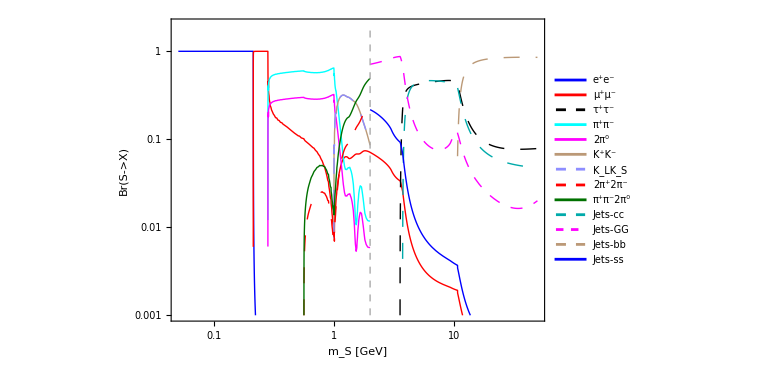

```mathematica
LogLogPlot[Evaluate[ListBrRatios["Scalar",mLLP,#]&/@ProcessesList["Scalar","True"]],{mLLP,0.05,50},Frame->True,ImageSize->Large,PlotLegends->Placed[LineLegend[Style[#,14]&/@(ProcessesList["Scalar","True"]),LegendLayout->{"Column",1}],{0.15,0.5}], FrameStyle->Directive[Black, 22],PlotRange->{{0.05,50},{10^-3,2}},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Brown},{Thick,Lighter@Lighter@Blue,Dashing[0.02]},{Thick,Red,Dashing[0.02]},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.015]},{Thick,Lighter@Brown,Dashing[0.02]}},AspectRatio->0.66,ImageSize->Large,FrameLabel->{"m_S [GeV]","Br(S->X)"}(*,PlotLabel->Style[Row[{"Decay branching ratios of dark photons"}],18,Black]*),PlotPoints->100,Epilog->{{Thick,Lighter@Gray,Dashed,Line[{{Log[2],Log[10^-3]},{Log[2],Log[2]}}]}}]
```

## DP

### List of decay processes, sets of decay products for them, squared matrix elements, branching ratios

```mathematica
LLPsel="DP";
BrRatiosDPdata[mLLP_,E1_,E3_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology",LLPsel,"decay widths/BrRatiosDP.mx"}],"MX"];
(*List of all representative processes*)
ProcessesList[LLPsel,"True"]=BrRatiosDPdata[mLLP,E1,E3][[All,1]]
Do[
Module[{proc},
proc=BrRatiosDPdata[mLLP,E1,E3][[i]][[1]];
ListDecayProducts[LLPsel,proc]=BrRatiosDPdata[mLLP,E1,E3][[i]][[2]];
JetsPresence[LLPsel,proc]=If[StringContainsQ[proc,"Jets"],"Yes","No"];
ListBrRatios[LLPsel,mLLP_,proc]=ListBrRatiosTemp[LLPsel,mLLP_,proc]=BrRatiosDPdata[mLLP,E1,E3][[i]][[3]];
If[Length[Select[ListDecayProducts[LLPsel,proc],#!="Null"&]]==3,
Msquared3BodyLLP[LLPsel,proc,E1_,E3_,mLLP_]=BrRatiosDPdata[mLLP,E1,E3][[i]][[4]];
];
]
,{i,1,Length[BrRatiosDPdata[mLLP,E1,E3]],1}]
Do[ListBrRatios[LLPsel,mLLP_,proc]=ListBrRatiosTemp[LLPsel,mLLP,proc]/Sum[ListBrRatiosTemp[LLPsel,mLLP,pr],{pr,ProcessesList[LLPsel,"True"]}]
,{proc,ProcessesList[LLPsel,"True"]}]
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
```

{K_LK_S,K^+K^-,K^+K^-π^0,K_SK^-π^+,K_SK^+π^-,π^+π^-π^0,π^+π^-π^+π^-,π^+π^-,ω_other,ϕ_other,(ρ^0)_other,π^0γ,π^+π^-π^0π^0,e-pair,μ-pair,τ-pair,Jets-uu,Jets-dd,Jets-ss,Jets-cc}

All processes with at least two charged particles:

{K_LK_S,K^+K^-,K^+K^-π^0,K_SK^-π^+,K_SK^+π^-,π^+π^-π^0,π^+π^-π^+π^-,π^+π^-,ω_other,ϕ_other,(ρ^0)_other,π^+π^-π^0π^0,e-pair,μ-pair,τ-pair,Jets-uu,Jets-dd,Jets-ss,Jets-cc}

Processes with jets:

{Jets-uu,Jets-dd,Jets-ss,Jets-cc}

#### Plot

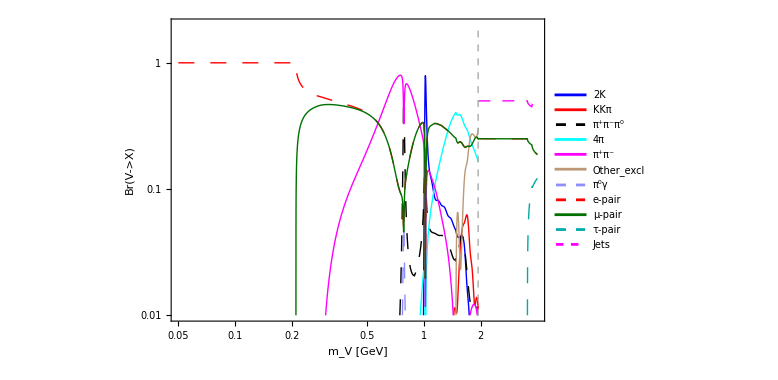

```mathematica
ProcessesListRefined["DP","True"]={"2K","KKπ","π^+π^-π^0","4π","π^+π^-","Other_excl","π^0γ","e-pair","μ-pair","τ-pair","Jets"};
Do[ListBrRatiosRefined["DP",mLLP_,proc]=ListBrRatios["DP",mLLP,proc],{proc,{"π^+π^-π^0","π^+π^-","π^0γ","e-pair","μ-pair","τ-pair","Jets"}}];
BrRefining[procref_,procslist_]:=ListBrRatiosRefined["DP",mLLP_,procref]=Sum[ListBrRatios["DP",mLLP,proc],{proc,procslist}]
{BrRefining["2K",{"K^+K^-","K_LK_S"}],BrRefining["KKπ",{"K^+K^-π^0","K_SK^-π^+","K_SK^+π^-"}],BrRefining["4π",{"π^+π^-π^+π^-","π^+π^-π^0π^0"}],BrRefining["Other_excl",{"ω_other","ϕ_other","(ρ^0)_other"}],BrRefining["Jets",{"Jets-uu","Jets-dd","Jets-ss","Jets-cc"}]};
LogLogPlot[Evaluate[ListBrRatiosRefined["DP",mLLP,#]&/@ProcessesListRefined["DP","True"]],{mLLP,0.05,4},Frame->True,ImageSize->Large,PlotLegends->Placed[LineLegend[Style[#,14]&/@(ProcessesListRefined["DP","True"]),LegendLayout->{"Column",1}],{0.15,0.44}], FrameStyle->Directive[Black, 22],PlotRange->{{0.05,4},{10^-2,2}},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Black,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Lighter@Brown},{Thick,Lighter@Lighter@Blue,Dashing[0.02]},{Thick,Red,Dashing[0.02]},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.015]},{Thick,Lighter@Brown,Dashing[0.02]}},AspectRatio->0.66,ImageSize->Large,FrameLabel->{"m_V [GeV]","Br(V->X)"}(*,PlotLabel->Style[Row[{"Decay branching ratios of dark photons"}],18,Black]*),PlotPoints->100,Epilog->{{Thick,Lighter@Gray,Dashed,Line[{{Log[1.94],Log[10^-2]},{Log[1.94],Log[2]}}]}}]
```

## HNL

### List of decay processes and sets of decay products for them, branching ratios, and matrix elements

```mathematica
HNLsList={"HNL-mixing-e","HNL-mixing-mu","HNL-mixing-tau"};
HNLdecaypheno0[mLLP_,E1_,E3_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology/HNL/decay widths/HNLdecaysSensCalc.mx"}],"MX"];
(*Merging processes and charge conjugated ones, as for the practic purposes there is no difference*)proclist=HNLdecaypheno0[mLLP,E1,E3][[All,1]];
HNLdecaypheno[mLLP_,E1_,E3_]={};
Do[
Module[{procbar},
If[!StringContainsQ[proc,"bar"],
procbar=proc<>"bar";
stringproc[mLLP_,E1_,E3_]=Select[HNLdecaypheno0[mLLP,E1,E3],#[[1]]==proc||#[[1]]==procbar&];
HNLdecaypheno[mLLP_,E1_,E3_]=Join[HNLdecaypheno[mLLP,E1,E3],{{stringproc[mLLP,E1,E3][[1]][[1]],stringproc[mLLP,E1,E3][[1]][[2]],Total[stringproc[mLLP,E1,E3][[All,3]]],Total[stringproc[mLLP,E1,E3][[All,4]]],Total[stringproc[mLLP,E1,E3][[All,5]]],stringproc[mLLP,E1,E3][[1]][[6]],stringproc[mLLP,E1,E3][[1]][[7]],stringproc[mLLP,E1,E3][[1]][[8]]}}]
]
]
,{proc,proclist}]
(*e mixing*)
LLPsel=HNLsList[[1]];
{channelsnonzero[HNLsList[[1]],mLLP_,E1_,E3_],channelsnonzero[HNLsList[[2]],mLLP_,E1_,E3_],channelsnonzero[HNLsList[[3]],mLLP_,E1_,E3_]}=Table[Select[HNLdecaypheno[mLLP,E1,E3],!FreeQ[#[[i]],0]&][[All,{1,2,i,3+i}]],{i,{3,4,5}}];
Do[
ProcessesList[hnl,"True"]=channelsnonzero[hnl,mLLP,E1,E3][[All,1]];
Do[
Module[{proc},
proc=ProcessesList[hnl,"True"][[i]];
ListDecayProducts[hnl,proc]=channelsnonzero[hnl,mLLP,E1,E3][[i]][[2]];
JetsPresence[hnl,proc]=If[StringContainsQ[proc,"Jets"],"Yes","No"];
ListBrRatios[hnl,mLLP_,proc]=ListBrRatiosTemp[hnl,mLLP_,proc]=channelsnonzero[hnl,mLLP,E1,E3][[i]][[3]];
If[Length[Select[ListDecayProducts[hnl,proc],#!="Null"&]]==3,
Msquared3BodyLLP[hnl,proc,E1_,E3_,mLLP_]=channelsnonzero[hnl,mLLP,E1,E3][[i]][[4]];
];
]
,{i,1,Length[ProcessesList[hnl,"True"]],1}]
,{hnl,HNLsList}]
Do[
ProcessesList[hnl,"False"]=procListnoecal[hnl]
,{hnl,HNLsList}]
```

#### Mixing e

All processes with at least two charged/neutral particles:

2ev | 2muv | 2Pie | 2Piv | 2tauv | a1v | emuv | EtaPrv | etauv | Etav | Jets-ccv | Jets-cse | Jets-ddv | Jets-ssv | Jets-ude | Jets-uuv | Ke | Omegav | Phiv | Pi0v | Pie
e^-
ν_e
e^+
Null | μ^-
ν_e
μ^+
Null | π^+
π^0
e^-
Null | π^+
π^0
ν_τ
Null | τ^-
ν_e
τ^+
Null | a_1
ν_e
Null
Null | e^-
(ν̄)_e
μ^+
Null | η'
ν_e
Null
Null | e^-
(ν̄)_e
τ^+
Null | η
ν_e
Null
Null | c
c̄
ν_e
Null | c
s̄
e^-
Null | d
d̄
ν_e
Null | s
s̄
ν_e
Null | u
d̄
e^-
Null | u
ū
ν_e
Null | K^+
e^-
Null
Null | ω
ν_e
Null
Null | ϕ
ν_e
Null
Null | π^0
ν_e
Null
Null | π^+
e^-
Null
Null

All processes with at least two charged particles:

{2ev,2muv,2Pie,2Piv,2tauv,a1v,emuv,EtaPrv,etauv,Etav,Jets-ccv,Jets-cse,Jets-ddv,Jets-ssv,Jets-ude,Jets-uuv,Ke,Omegav,Phiv,Pie}

Processes with jets:

{Jets-ccv,Jets-cse,Jets-ddv,Jets-ssv,Jets-ude,Jets-uuv}

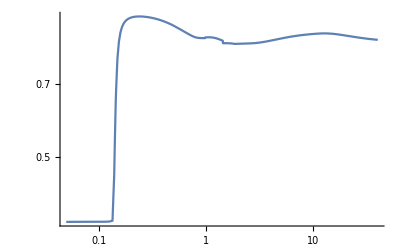

```mathematica
LLPsel=HNLsList[[1]];
Print["All processes with at least two charged/neutral particles:"]
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatios[LLPsel,mN,pr],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,40},PlotRange->All]
```

#### Mixing μ

All processes with at least two charged/neutral particles:

2ev | 2muv | 2Pimu | 2Piv | 2tauv | a1v | emuv | EtaPrv | Etav | Jets-ccv | Jets-csmu | Jets-ddv | Jets-ssv | Jets-udmu | Jets-uuv | Kmu | mutauv | Omegav | Phiv | Pi0v | Pimu
e^-
ν_e
e^+
Null | μ^-
ν_e
μ^+
Null | π^+
π^0
μ^-
Null | π^+
π^0
ν_τ
Null | τ^-
ν_e
τ^+
Null | a_1
ν_e
Null
Null | e^-
(ν̄)_e
μ^+
Null | η'
ν_e
Null
Null | η
ν_e
Null
Null | c
c̄
ν_e
Null | c
s̄
μ^-
Null | d
d̄
ν_e
Null | s
s̄
ν_e
Null | u
d̄
μ^-
Null | u
ū
ν_e
Null | K^+
μ^-
Null
Null | μ^-
(ν̄)_e
τ^+
Null | ω
ν_e
Null
Null | ϕ
ν_e
Null
Null | π^0
ν_e
Null
Null | π^+
μ^-
Null
Null

All processes with at least two charged particles:

{2ev,2muv,2Pimu,2Piv,2tauv,a1v,emuv,EtaPrv,Etav,Jets-ccv,Jets-csmu,Jets-ddv,Jets-ssv,Jets-udmu,Jets-uuv,Kmu,mutauv,Omegav,Phiv,Pimu}

Processes with jets:

{Jets-ccv,Jets-csmu,Jets-ddv,Jets-ssv,Jets-udmu,Jets-uuv}

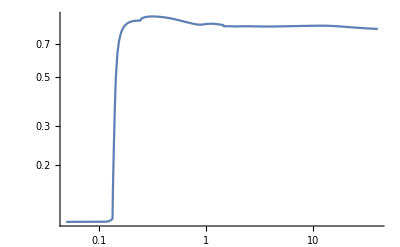

```mathematica
LLPsel=HNLsList[[2]];
Print["All processes with at least two charged/neutral particles:"]
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatios[LLPsel,mN,pr],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,40},PlotRange->All]
```

#### Mixing τ

All processes with at least two charged/neutral particles:

2ev | 2muv | 2Pitau | 2Piv | 2tauv | a1v | EtaPrv | etauv | Etav | Jets-ccv | Jets-cstau | Jets-ddv | Jets-ssv | Jets-udtau | Jets-uuv | Ktau | mutauv | Omegav | Phiv | Pi0v | Pitau
e^-
ν_e
e^+
Null | μ^-
ν_e
μ^+
Null | π^+
π^0
τ^-
Null | π^+
π^0
ν_τ
Null | τ^-
ν_e
τ^+
Null | a_1
ν_e
Null
Null | η'
ν_e
Null
Null | e^-
(ν̄)_e
τ^+
Null | η
ν_e
Null
Null | c
c̄
ν_e
Null | c
s̄
τ^-
Null | d
d̄
ν_e
Null | s
s̄
ν_e
Null | u
d̄
τ^-
Null | u
ū
ν_e
Null | K^+
τ^-
Null
Null | μ^-
(ν̄)_e
τ^+
Null | ω
ν_e
Null
Null | ϕ
ν_e
Null
Null | π^0
ν_e
Null
Null | π^+
τ^-
Null
Null

All processes with at least two charged particles:

{2ev,2muv,2Pitau,2Piv,2tauv,a1v,EtaPrv,etauv,Etav,Jets-ccv,Jets-cstau,Jets-ddv,Jets-ssv,Jets-udtau,Jets-uuv,Ktau,mutauv,Omegav,Phiv,Pitau}

Processes with jets:

{Jets-ccv,Jets-cstau,Jets-ddv,Jets-ssv,Jets-udtau,Jets-uuv}

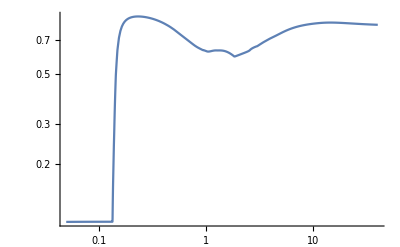

```mathematica
LLPsel=HNLsList[[3]];
Print["All processes with at least two charged/neutral particles:"]
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatios[LLPsel,mN,pr],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,40},PlotRange->All]
```

## ALPs coupled to gluons

### List of decay processes and sets of decay products for them, branching ratios

2e | 2μ | 2τ | 2γ | π^+π^-π^0 | γπ^+π^- | π^+π^-2π^0 | 2π^+2π^- | η2π^0 | ηπ^+π^- | K^(*+)K^(*-) | K^(*0)(K̄)^(*0) | K^0(K̄)^0π^0 | K^-K^0π^+ | K^+K^-π^0 | K^+(K̄)^0π^- | ωπ^+π^- | 3π^0 | η'2π^0 | η'π^+π^- | 2ω | Jets-GG | Jets-cc | Jets-ss
e^+
e^-
Null
Null | μ^+
μ^-
Null
Null | τ^+
τ^-
Null
Null | γ
γ
Null
Null | π^+
π^-
π^0
Null | π^+
π^-
γ
Null | π^+
π^0
π^-
π^0 | π^+
π^-
π^+
π^- | η
π^0
π^0
Null | η
π^+
π^-
Null | K^(*+)
K^(*-)
Null
Null | K^(*0)
(K̄)^(*0)
Null
Null | K_L
K_S
π^0
Null | K^-
K_L
π^+
Null | K^+
K^-
π^0
Null | K^+
K_S
π^-
Null | ω
π^+
π^-
Null | π^0
π^0
π^0
Null | η'
π^0
π^0
Null | η'
π^+
π^-
Null | ω
ω
Null
Null | g
ḡ
Null
Null | c
c̄
Null
Null | s
s̄
Null
Null

All processes with at least two charged/neutral particles:

{2e,2μ,2τ,2γ,π^+π^-π^0,γπ^+π^-,π^+π^-2π^0,2π^+2π^-,η2π^0,ηπ^+π^-,K^(*+)K^(*-),K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,ωπ^+π^-,3π^0,η'2π^0,η'π^+π^-,2ω,Jets-GG,Jets-cc,Jets-ss}

All processes with at least two charged particles:

{2e,2μ,2τ,π^+π^-π^0,γπ^+π^-,π^+π^-2π^0,2π^+2π^-,η2π^0,ηπ^+π^-,K^(*+)K^(*-),K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,ωπ^+π^-,η'2π^0,η'π^+π^-,2ω,Jets-GG,Jets-cc,Jets-ss}

Processes with jets:

{Jets-GG,Jets-cc,Jets-ss}

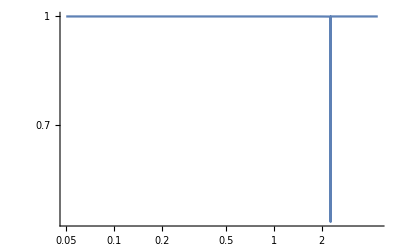

```mathematica
LLPsel="ALP-gluon";
BrRatiosALPgluonData[ma_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology",LLPsel,"decay widths/Br-ratios-SensCalc-model-Gluon-scale-1000.-GeV.m"}],"MX"];
(*List of all representative processes*)
ProcessesList[LLPsel,"True"]=BrRatiosALPgluonData[ma][[1]]/.{"Jets"->"Jets-GG"};
(*The mass above which all hadronic decays are approximated by decays into jets*)
Do[
procsel=ProcessesList[LLPsel,"True"][[i]];
ListBrRatiosTemp[LLPsel,mLLP_,procsel]=ListBrRatios[LLPsel,mLLP_,procsel]=BrRatiosALPgluonData[mLLP][[3]][[i]];
ListDecayProducts[LLPsel,procsel]=BrRatiosALPgluonData[ma][[2]][[i]];
JetsPresence[LLPsel,procsel]=If[MemberQ[{"Jets-ss","Jets-cc","Jets-GG"},procsel]==True,"Yes","No"]
,{i,1,Length[BrRatiosALPgluonData[mLLP][[3]]],1}]
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel];
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm
Print["All processes with at least two charged/neutral particles:"]
ProcessesList[LLPsel,"True"]
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatiosTemp[LLPsel,mN,pr],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,4.5},PlotRange->All]
```

### Squared matrix elements

```mathematica
LLPsel="ALP-gluon";
MatrixElementsALPgluonList[ma_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology",LLPsel,"decay widths/Matrix-elements-squared-model-Gluon-scale-1000.-GeV.m"}],"MX"];
Do[Msquared3BodyLLP[LLPsel,MatrixElementsALPgluonList[ma][[1]][[i]],E1_,E3_,mLLP_]=MatrixElementsALPgluonList[mLLP][[3]][[i]]
,{i,1,Length[MatrixElementsALPgluonList[ma][[3]]],1}];
```

## ALPs coupled to fermions

### List of decay processes and sets of decay products for them, branching ratios

All processes with at least two charged/neutral particles:

{2e,2μ,2τ,2γ,π^+π^-π^0,γπ^+π^-,π^+π^-2π^0,2π^+2π^-,η2π^0,ηπ^+π^-,K^(*+)K^(*-),K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,ωπ^+π^-,3π^0,η'2π^0,η'π^+π^-,2ω,Jets-GG,Jets-cc,Jets-ss}

All processes with at least two charged particles:

{2e,2μ,2τ,π^+π^-π^0,γπ^+π^-,π^+π^-2π^0,2π^+2π^-,η2π^0,ηπ^+π^-,K^(*+)K^(*-),K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,ωπ^+π^-,η'2π^0,η'π^+π^-,2ω,Jets-GG,Jets-cc,Jets-ss}

Processes with jets:

{Jets-GG,Jets-cc,Jets-ss}

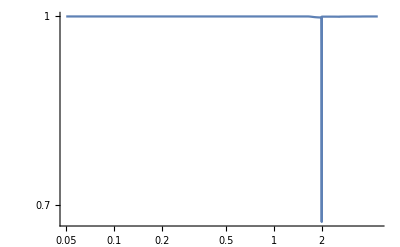

```mathematica
LLPsel="ALP-fermion";
BrRatiosALPfermionData[ma_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology",LLPsel,"decay widths/Br-ratios-SensCalc-model-Fermion universal-scale-1000.-GeV.m"}],"MX"];
(*List of all representative processes*)
ProcessesList[LLPsel,"True"]=BrRatiosALPfermionData[ma][[1]]/.{"Jets"->"Jets-GG"};
(*The mass above which all hadronic decays are approximated by decays into jets*)
Do[
procsel=ProcessesList[LLPsel,"True"][[i]];
ListBrRatiosTemp[LLPsel,mLLP_,procsel]=ListBrRatios[LLPsel,mLLP_,procsel]=BrRatiosALPfermionData[mLLP][[3]][[i]];
ListDecayProducts[LLPsel,procsel]=BrRatiosALPfermionData[ma][[2]][[i]];
JetsPresence[LLPsel,procsel]=If[MemberQ[{"Jets-ss","Jets-cc","Jets-GG"},procsel]==True,"Yes","No"]
,{i,1,Length[BrRatiosALPfermionData[mLLP][[3]]],1}]
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel];
Print["All processes with at least two charged/neutral particles:"]
ProcessesList[LLPsel,"True"]
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatiosTemp[LLPsel,mN,pr],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,4.5},PlotRange->All]
```

```mathematica
(*malist=Table[ma,{ma,0.3,5.2,0.001}];
tabbr=(Join[Partition[malist,1],Table[(BrRatiosALPfermionData[ma][[3]])/Total[BrRatiosALPfermionData[ma][[3]]],{ma,malist}],2]/. x_Real/;Abs[x]<10^-15:>0.)//N//Developer`ToPackedArray;
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"temp1","br-ratios-BC10.txt"}],tabbr,"Table"]*)
```

#### Old description from 1901.09966 - no hadronic decays

All processes with at least two charged/neutral particles:

{2e,2μ,2τ}

All processes with at least two charged particles:

{2e,2μ,2τ}

Processes with jets:

{}

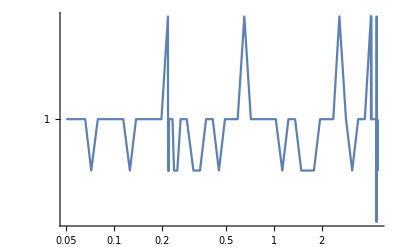

```mathematica
LLPsel="ALP-fermion-no-hadronic-decays";
(*List of all representative processes*)
ProcessesList[LLPsel,"True"]=Select[ProcessesList["ALP-fermion","True"],MemberQ[{"2e","2μ","2τ"},#]==True&];
(*The mass above which all hadronic decays are approximated by decays into jets*)
Do[
procsel=ProcessesList[LLPsel,"True"][[i]];
ListBrRatiosTemp[LLPsel,mLLP_,procsel]=ListBrRatios[LLPsel,mLLP_,procsel]=ListBrRatios["ALP-fermion",mLLP,procsel]/(ListBrRatios["ALP-fermion",mLLP,"2e"]+ListBrRatios["ALP-fermion",mLLP,"2μ"]+ListBrRatios["ALP-fermion",mLLP,"2τ"])//Simplify;
ListDecayProducts[LLPsel,procsel]=ListDecayProducts["ALP-fermion",procsel];
JetsPresence[LLPsel,procsel]=If[procsel=="Jets-GG","Yes","No"]
,{i,1,Length[ProcessesList[LLPsel,"True"]],1}]
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel];
Print["All processes with at least two charged/neutral particles:"]
ProcessesList[LLPsel,"True"]
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatiosTemp[LLPsel,mN,pr],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,4.5},PlotRange->All]
```

### Squared matrix elements

```mathematica
LLPsel="ALP-fermion";
MatrixElementsALPfermionList[ma_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology",LLPsel,"decay widths/Matrix-elements-squared-model-Fermion universal-scale-1000.-GeV.m"}],"MX"];
Do[Msquared3BodyLLP[LLPsel,MatrixElementsALPfermionList[ma][[1]][[i]],E1_,E3_,mLLP_]=MatrixElementsALPfermionList[mLLP][[3]][[i]]
,{i,1,Length[MatrixElementsALPfermionList[ma][[3]]],1}];
```

## B-L_α mediator

```mathematica
Print["List of available models:"]
modelsBL=StringReplace[FileBaseName[#],"BrRatios-"->""]&/@FileNames["BrRatios-*.mx",FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology","B-L","decay widths"}]]//DeleteDuplicates
Do[
BrRatiosBLdata[mLLP_,E1_,E3_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology","B-L","decay widths/BrRatios-"<>model<>".mx"}],"MX"];
(*List of all representative processes*)
ProcessesList[model,"True"]=BrRatiosBLdata[mLLP,E1,E3][[All,1]];
Do[
Module[{proc},
proc=BrRatiosBLdata[mLLP,E1,E3][[i]][[1]];
ListDecayProducts[model,proc]=BrRatiosBLdata[mLLP,E1,E3][[i]][[2]];
JetsPresence[model,proc]=If[StringContainsQ[proc,"Jets"],"Yes","No"];
ListBrRatios[model,mLLP_,proc]=ListBrRatiosTemp[model,mLLP_,proc]=BrRatiosBLdata[mLLP,E1,E3][[i]][[3]];
If[Length[Select[ListDecayProducts[model,proc],#!="Null"&]]==3,
Msquared3BodyLLP[model,proc,E1_,E3_,mLLP_]=BrRatiosBLdata[mLLP,E1,E3][[i]][[4]];
];
]
,{i,1,Length[BrRatiosBLdata[mLLP,E1,E3]],1}];
Do[ListBrRatios[model,mLLP_,proc]=ListBrRatiosTemp[model,mLLP,proc]/Sum[ListBrRatiosTemp[model,mLLP,pr],{pr,ProcessesList[model,"True"]}]
,{proc,ProcessesList[model,"True"]}];
ProcessesList[model,"False"]=procListnoecal[model]
,{model,modelsBL}]
Print["All processes with at least two charged particles for B-L:"]
ProcessesList["B-L","False"]
Print["Processes with jets:"]
Select[ProcessesList["B-L","True"],JetsPresence["B-L",#]=="Yes"&]
```

List of available models:

{B-3Le-Lmu+Ltau,B-3Lmu,B-Le-3Lmu+Ltau,B-L}

All processes with at least two charged particles for B-L:

{Jets-cc,Jets-dd,Jets-ss,Jets-uu,K_LK_S,K_SK^-π^+,K_SK^+π^-,e^+e^-,K^+K^-,K^+K^-π^0,μ^+μ^-,π^+π^-π^0,τ^+τ^-}

Processes with jets:

{Jets-cc,Jets-dd,Jets-ss,Jets-uu}

## ALPs coupled to photons

### List of decay processes and sets of decay products for them, branching ratios

```mathematica
LLPsel="ALP-photon"
{ListBrRatiosTemp["ALP-photon",mLLP_,"γ-pair"],ListDecayProducts["ALP-photon","γ-pair"],JetsPresence["ALP-photon","γ-pair"]}={1,{"γ","γ","Null","Null"},"No"};
ListBrRatios["ALP-photon",mLLP_,"γ-pair"]=ListBrRatiosTemp["ALP-photon",mLLP,"γ-pair"];
Print["All processes with at least two charged/neutral particles:"]
ProcessesList[LLPsel,"True"]=procList[LLPsel]
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
```

ALP-photon

All processes with at least two charged/neutral particles:

{γ-pair}

All processes with at least two charged particles:

{}

Processes with jets:

{}

### Matrix elements

## LLPs - total

```mathematica
LLPlist=Keys[DownValues@ProcessesList][[All,1,1]]//DeleteDuplicates
(*If decay products may be uncharged only/metastable decay product itself is uncharged*)
OnlyUnch["ω"]=0;
OnlyUnch["ρ^0"]=0;
OnlyUnch["η"]=0;
OnlyUnch["η'"]=0;
OnlyUnch["π^0"]=1;
OnlyUnch["K_L"]=1;
OnlyUnch["K_S"]=0;
OnlyUnch["K^(*0)"]=OnlyUnch["(K̄)^(*0)"]=0;
OnlyUnch["a_1"]=0;
OnlyUnch["ϕ"]=0;
(*The probability with which the given decay products will give at least two charged tracks*)
ecalfactor[LLP_,proc_]:=Block[{},
decayprodlist=Select[ListDecayProducts[LLP,proc],#!="Null"&];
decayprodpdglist=ParamProductToPDGid[#]&/@decayprodlist;
chargedprodscounter=Sum[If[ParamProductCharge[decayprodpdglist[[i]]]!=0.,1,0],{i,1,Length[decayprodpdglist]}];
If[chargedprodscounter>=2,val=1,
stability=ParamProductStability[#]&/@decayprodpdglist;
val=1-Product[If[stability[[i]]==0.,OnlyUnch[decayprodlist[[i]]],1],{i,1,Length[decayprodlist],1}]
];
val
]
Join[{{"LLP","Process","P_(> 2 charged particles)"}},Flatten[Table[{LLP,proc,ecalfactor[LLP,proc]},{LLP,LLPlist},{proc,ProcessesList[LLP,"True"]}],{1,2}]];
BrVisibleGivenSetup[LLP_,mLLP_,proclist_,ECALoption_]:=Block[{},
Sum[ListBrRatios[LLP,mLLP,proclist[[i]]]*If[ECALoption=="True",1,ecalfactor[LLP,proclist[[i]]]],{i,1,Length[proclist],1}]
]
```

{ALP-fermion,ALP-fermion-no-hadronic-decays,ALP-gluon,ALP-photon,B-3Le-Lmu+Ltau,B-3Lmu,B-L,B-Le-3Lmu+Ltau,DP,HNL-mixing-e,HNL-mixing-mu,HNL-mixing-tau,Scalar}

## Unstable SM particles

### List of decay processes and decay products

#### τ leptons

```mathematica
{ListDecayProducts["τ^+","eνν"],ListDecayProducts["τ^+","μνν"],ListDecayProducts["τ^+","πν"],ListDecayProducts["τ^+","2πν"]}={{"e^+","ν_e","(ν̄)_τ","Null"},{"μ^+","ν_μ","(ν̄)_τ","Null"},{"π^+","(ν̄)_τ","Null","Null"},{"π^+","π^0","(ν̄)_τ","Null"}};
{ListDecayProducts["τ^-","eνν"],ListDecayProducts["τ^-","μνν"],ListDecayProducts["τ^-","πν"],ListDecayProducts["τ^-","2πν"]}={{"e^-","(ν̄)_e","ν_τ","Null"},{"μ^-","(ν̄)_μ","ν_τ","Null"},{"π^-","ν_τ","Null","Null"},{"π^-","π^0","ν_τ","Null"}};
{ωprocess["τ^+","eνν"],ωprocess["τ^+","μνν"],ωprocess["τ^+","πν"],ωprocess["τ^+","2πν"]}={ωprocess["τ^-","eνν"],ωprocess["τ^-","μνν"],ωprocess["τ^-","πν"],ωprocess["τ^-","2πν"]}={0.1739,0.1782,0.1082,0.2549};
```

#### η,η',π^0

```mathematica
{ListDecayProducts["η","π^+π^-π^0"],ListDecayProducts["η","3π^0"],ListDecayProducts["η","γ-pair"]}={ {"π^+","π^-","π^0","Null"},{"π^0","π^0","π^0","Null"},{"γ","γ","Null","Null"}};
{ωprocess["η","π^+π^-π^0"],ωprocess["η","3π^0"],ωprocess["η","γ-pair"]}={0.2302,0.3257,0.3936};
{ListDecayProducts["η'","π^+π^-η"],ListDecayProducts["η'","ρ^0γ"],ListDecayProducts["η'","2π^0η"]}={ {"π^+","π^-","η","Null"},{"ρ^0","γ","Null","Null"},{"π^0","π^0","η","Null"}};
{ωprocess["η'","π^+π^-η"],ωprocess["η'","ρ^0γ"],ωprocess["η'","2π^0η"]}={0.425,0.295,0.224};
ListDecayProducts["π^0","γ-pair"]={"γ","γ","Null","Null"};
ωprocess["π^0","γ-pair"]=1;
```

#### ρ, ω, ϕ, a_1

```mathematica
{ListDecayProducts["ρ^+","π^+π^0"],ListDecayProducts["ρ^-","π^-π^0"],ListDecayProducts["ρ^0","π^charged-pair"]}={{"π^+","π^0","Null","Null"},{"π^-","π^0","Null","Null"},{"π^+","π^-","Null","Null"}};
{ωprocess["ρ^+","π^+π^0"],ωprocess["ρ^-","π^-π^0"],ωprocess["ρ^0","π^charged-pair"]}={1,1,1};
{ListDecayProducts["ω","π^+π^-π^0"],ListDecayProducts["ω","πγ"]}={{"π^+","π^-","π^0","Null"},{"π^0","γ","Null","Null"}};
{ωprocess["ω","π^+π^-π^0"],ωprocess["ω","πγ"]}={0.892,0.0835};
{ListDecayProducts["ϕ","ρ^-π^+"],ListDecayProducts["ϕ","ρ^+π^-"],ListDecayProducts["ϕ","K^+K^-"],ListDecayProducts["ϕ","2K^0"]}={{"ρ^-","π^+","Null","Null"},{"ρ^+","π^-","Null","Null"},{"K^+","K^-","Null","Null"},{"K_L","K_S","Null","Null"}};
{ωprocess["ϕ","ρ^-π^+"],ωprocess["ϕ","ρ^+π^-"],ωprocess["ϕ","K^+K^-"],ωprocess["ϕ","2K^0"]}={0.1532/2,0.1532/2,0.489,0.342};
{ListDecayProducts["a_1","ρ^+π^-"],ListDecayProducts["a_1","ρ^-π^+"]}={{"ρ^+","π^-","Null","Null"},{"ρ^-","π^+","Null","Null"}};
{ωprocess["a_1","ρ^+π^-"],ωprocess["a_1","ρ^-π^+"]}={0.5,0.5};
```

#### K^*,K_S

```mathematica
{ListDecayProducts["K^(*+)","K^+π^0"],ListDecayProducts["K^(*-)","K^-π^0"],ListDecayProducts["K^(*0)","K^+π^-"],ListDecayProducts["(K̄)^(*0)","K^-π^+"]}={{"K^+","π^0","Null","Null"},{"K^-","π^0","Null","Null"},{"K^+","π^-","Null","Null"},{"K^-","π^+","Null","Null"}};
{ωprocess["K^(*+)","K^+π^0"],ωprocess["K^(*-)","K^-π^0"],ωprocess["K^(*0)","K^+π^-"],ωprocess["(K̄)^(*0)","K^-π^+"]}={1,1,1,1};
{ListDecayProducts["K_S","π^+π^-"],ListDecayProducts["K_S","2π^0"]}={{"π^+","π^-","Null","Null"},{"π^0","π^0","Null","Null"}};
{ωprocess["K_S","π^+π^-"],ωprocess["K_S","2π^0"]}={0.6920,0.3069};
```

### Matrix elements

```mathematica
ListSMdecays=Join[Partition[Keys[DownValues@ωprocess][[All,1,1]],1],Partition[Keys[DownValues@ωprocess][[All,1,2]],1],2];
Do[Msquared3BodySMparticles[ListSMdecays[[i]][[1]],ListSMdecays[[i]][[2]],E1_,E3_,m_]=1,{i,1,Length[ListSMdecays],1}]
(*Table[With[{part=ListSMdecays[[i]][[1]],proc=ListSMdecays[[i]][[2]]},Evaluate[{part,proc,ListDecayProducts[part,proc][[1]],ListDecayProducts[part,proc][[2]],ListDecayProducts[part,proc][[3]],ListDecayProducts[part,proc][[4]],ωprocess[part,proc]}]],{i,1,Length[ListSMdecays],1}]*)
```

## Phase space of decay products at the rest frame of the decaying LLP

## Phase space of decay products - generated on-flight

### Phase space of LLP’s decays at its rest frame - 2-body decays

```mathematica
(*Computation of the phase space of 2-body products: 4-momenta, mass, pdg, electric charge, whether stable or not*)
nVectorParticles=Compile[{{θvals,_Real},{ϕvals,_Real},{E1,_Real},{E2,_Real},{m1,_Real},{m2,_Real},{pdg1,_Real},{pdg2,_Real},{charge1,_Real},{charge2,_Real},{stability1,_Real},{stability2,_Real}},
Module[{pmod,px1,px2,py1,py2,pz1,pz2},
pmod=√(E1^2-m1^2);
px1=pmod*Sin[θvals]*Cos[ϕvals];
px2=-px1;
py1=pmod*Sin[θvals]*Sin[ϕvals];
py2=-py1;
pz1=pmod*Cos[θvals];
pz2=-pz1;
{px1,py1,pz1,E1,m1,pdg1,charge1,stability1,px2,py2,pz2,E2,m2,pdg2,charge2,stability2}
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}];
joincompiled=Compile[{{tab1,_Real,2},{tab2,_Real,2},{tab3,_Real,2}},Join[tab1[[All,{1,2,3,4,5}]],tab2,tab1[[All,{6,7,8,9,10}]],tab3,2],CompilationTarget->"C",RuntimeOptions->"Speed"]
Block2BodyDistrAtRest[m_,product1_,product2_,Nevents_]:=Module[{θtab,ϕtab,E1v,E2v,mass1,mass2,pdg1,pdg2,charge1,charge2,stability1,stability2},
{pdg1,pdg2}=ParamProductToPDGid[#]&/@{product1,product2};
{mass1,mass2}=ParamProductMass[#]&/@{pdg1,pdg2};
{charge1,charge2}=ParamProductCharge[#]&/@{pdg1,pdg2};
{stability1,stability2}=ParamProductStability[#]&/@{pdg1,pdg2};
(*Random values of θ and ϕ. For θ, the distribution in cosθ is uniform, hence one first generates random values from -1 to 1 and then computes ArcCos*)
θtab=ArcCos[RandomReal[{-1,1},Nevents]];
ϕtab=RandomReal[{-Pi,Pi},Nevents];
{E1v,E2v}={(m^2+mass1^2-mass2^2)/(2*m),(m^2+mass2^2-mass1^2)/(2*m)};
nVectorParticles[θtab,ϕtab,E1v,E2v,mass1,mass2,pdg1,pdg2,charge1,charge2,stability1,stability2]]
(*Columns for the decay product phase space expressed in terms of 4-momenta*)
indexpx1=1;
indexpy1=2;
indexpz1=3;
indexE1=4;
indexm1=5;
indexpdg1=6;
indexcharge1=7;
indexstability1=8;
LengthDataProduct=indexstability1;
```

### Phase space of LLP’s decays at its rest frame - 3-body decays

```mathematica
BlockRandomEnergiesOld=Compile[{m,m1,m2,m3},Module[{E1r=0.,E2v=0.,E3r=0.},While[E3r=RandomReal[{m3,(m^2+m3^2-(m1+m2)^2)/(2*m)}];
E1r=RandomReal[{m1,(m^2+m1^2-(m2+m3)^2)/(2*m)}];
E2v=m-E1r-E3r;
E2v≤m2||(E2v^2-m2^2-(E1r^2-m1^2)-(E3r^2-m3^2))^2≥4*(E1r^2-m1^2)*(E3r^2-m3^2)];
{E1r,E3r}],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True];
BlockRandomEnergiesOld1=With[{br=BlockRandomEnergiesOld},Hold@Compile[{m,m1,m2,m3,{Nevents,_Integer}},Table[br[m,m1,m2,m3],Nevents],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True,CompilationOptions->{"InlineCompiledFunctions"->True}]//ReleaseHold];
(*The idea (following "Particle kinematics" by Byckling and Kajantie):*)
(*Generate the random energies Subscript[E, 1],Subscript[E, 3] with the weight being the squared matrix element of the decay process*)
(*Restore full 4-momenta*)
NN=10^5;
(*The routine that computes the weights M^2(Subscript[E, 1],Subscript[E, 3])Subscript[ΔE, 3](Subscript[E, 1]) for the given uniformly distributed Subscript[E, 1],Subscript[E, 3]*)
weightsNonUniformComp:=Hold@Compile[{{tabe1e3,_Real,1},MASSM,MASS1,MASS2,MASS3},Module[{e1,e3},
e1=Compile`GetElement[tabe1e3,1];
e3=Compile`GetElement[tabe1e3,2];
distr[e1,e3](**ΔE3[e1,MASSM,MASS1,MASS2,MASS3]*)
],CompilationTarget->"MVM",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/.ruleDown[{distr(*,ΔE3*)}]//ReleaseHold;
weightsUniformComp=Hold@Compile[{{tabe1e3,_Real,1},MASSM,MASS1,MASS2,MASS3},Module[{e1,e3},
e1=Compile`GetElement[tabe1e3,1];
ΔE3[e1,MASSM,MASS1,MASS2,MASS3]
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/.ruleDown[{ΔE3}]//ReleaseHold;
E3valsComp=Hold@Compile[{{E1vals,_Real},MASSM,MASS1,MASS2,MASS3},Module[{e3max,e3min},
e3min=E3domainMin[E1vals,MASSM,MASS1,MASS2,MASS3];
e3max=E3domainMax[E1vals,MASSM,MASS1,MASS2,MASS3];
RandomReal[{e3min,e3max}]
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/.ruleDown[{E3domainMax,E3domainMin}]//ReleaseHold;
BlockRandomEnergies[m_,m1_,m2_,m3_,Nevents_,distr_]:=Block[{},
(*E1maxval=E1domainMax[m,m1,m2,m3];
E1vals=RandomReal[{m1,E1maxval},Max[NN,Nevents]];
E3vals=E3valsComp[E1vals,m,m1,m2,m3];
tabE1E3unweighted={E1vals,E3vals}//Transpose;*)
(*Weights for the generated values of {E1,E3} from matrix element squared*)
If[distr[RandomReal[{m1,E1domainMax[m,m1,m2,m3]}],RandomReal[{m3,(m^2+m3^2-(m1+m2)^2)/(2*m)}]]!=1,
(*Table with random energies distributed in the Dalitz range before accounting for weights*)
tabE1E3unweighted=BlockRandomEnergiesOld1[m,m1,m2,m3,Max[Nevents,NN]];
(*Weights from matrix element*)
weights1=weightsNonUniformComp;
weights=Abs[weights1[tabE1E3unweighted,m,m1,m2,m3](*/._?Negative->0*)];
(*True random energies. Computed via empirical distribution from the weigthed data*)
tabsel=RandomChoice[weights->tabE1E3unweighted,Nevents];
,
tabsel=BlockRandomEnergiesOld1[m,m1,m2,m3,Nevents];
];
tabsel
(*(*Weighted random points*)
weightedData=WeightedData[tabE1E3unweighted,weights];
(*True random energies. Computed via empirical distribution from the weigthed data*)
edist=EmpiricalDistribution[weightedData];
RandomVariate[edist,Nevents];*)
]
(*Phase space of 3-body decays at rest. Returns blocks with the following data: productdata = Subscript[p, x],Subscript[p, y],Subscript[p, z],E,m,pdg,charge,stability*)
tabPS3bodyCompiled=Hold@Compile[{{tabPSenergies,_Real,1},{MASSM,_Real},{MASS1,_Real},{MASS2,_Real},{MASS3,_Real},{pdg1,_Real},{pdg2,_Real},{pdg3,_Real},{charge1,_Real},{charge2,_Real},{charge3,_Real},{stability1,_Real},{stability2,_Real},{stability3,_Real}},
Module[{eprod1,eprod2,eprod3,pxprod1,pxprod2,pxprod3,pyprod1,pyprod2,pyprod3,pzprod1,pzprod2,pzprod3,θrandTab,ϕrandTab,κrandTab},
eprod1=Compile`GetElement[tabPSenergies,1];
eprod3=Compile`GetElement[tabPSenergies,2];
(*Angles relating generated energies to the 4-momenta*)
θrandTab=ArcCos[RandomReal[{-1,1}]];
ϕrandTab=RandomReal[{-Pi,Pi}];
κrandTab=RandomReal[{-Pi,Pi}];
eprod2=MASSM-eprod1-eprod3;
pxprod1=p1rotatedX[eprod1,MASS1,θrandTab,ϕrandTab];
pyprod1=p1rotatedY[eprod1,MASS1,θrandTab,ϕrandTab];
pzprod1=p1rotatedZ[eprod1,MASS1,θrandTab,ϕrandTab];
pxprod2=p2rotatedX[eprod1,eprod3,MASSM,MASS1,MASS2,MASS3,θrandTab,ϕrandTab,κrandTab];
pyprod2=p2rotatedY[eprod1,eprod3,MASSM,MASS1,MASS2,MASS3,θrandTab,ϕrandTab,κrandTab];
pzprod2=p2rotatedZ[eprod1,eprod3,MASSM,MASS1,MASS2,MASS3,θrandTab,ϕrandTab,κrandTab];
pxprod3=p3rotatedX[eprod1,eprod3,MASSM,MASS1,MASS2,MASS3,θrandTab,ϕrandTab,κrandTab];
pyprod3=p3rotatedY[eprod1,eprod3,MASSM,MASS1,MASS2,MASS3,θrandTab,ϕrandTab,κrandTab];
pzprod3=p3rotatedZ[eprod1,eprod3,MASSM,MASS1,MASS2,MASS3,θrandTab,ϕrandTab,κrandTab];
{pxprod1,pyprod1,pzprod1,eprod1,MASS1,pdg1,charge1,stability1,pxprod2,pyprod2,pzprod2,eprod2,MASS2,pdg2,charge2,stability2,pxprod3,pyprod3,pzprod3,eprod3,MASS3,pdg3,charge3,stability3}
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.ruleDown[{p1rotatedX,p1rotatedY,p1rotatedZ,p2rotatedX,p2rotatedY,p2rotatedZ,p3rotatedX,p3rotatedY,p3rotatedZ}]//ReleaseHold;
<<CompiledFunctionTools`
CompilePrint@tabPS3bodyCompiled;
ThreeBodyDecaysEventsAtRest[particle_,SpecificDecay_,mparticle_,Nevents_]:=Module[{(*pdg1,pdg2,pdg3,MASSM,MASS1,MASS2,MASS3,charge1,charge2,charge3,stability1,stability2,stability3,θrandTab,ϕrandTab,κrandTab,(*tabRPPS,weights1,weights,*)decayproductsset,weightedData,edist,tabPSenergies*)},
(*___________________________________*)
(*Extracting information about the decay*)
MASSM =If[!MemberQ[LLPlist,particle],ParamProductMass[ParamProductToPDGid[particle]],mparticle];
decayproductsset=Select[ListDecayProducts[particle,SpecificDecay],#!="Null"&];
{pdg1,pdg2,pdg3}=ParamProductToPDGid[#]&/@decayproductsset;
{MASS1,MASS2,MASS3}=ParamProductMass[#]&/@{pdg1,pdg2,pdg3};
{charge1,charge2,charge3}=ParamProductCharge[#]&/@{pdg1,pdg2,pdg3};
{stability1,stability2,stability3}=ParamProductStability[#]&/@{pdg1,pdg2,pdg3};
(*The squared matrix element for the process - to compute weights*)
distr[E1_,E3_]=If[!MemberQ[LLPlist,particle],Msquared3BodySMparticles[particle,SpecificDecay,E1,E3,MASSM],Msquared3BodyLLP[particle,SpecificDecay,E1,E3,MASSM]];
(*___________________________________*)
(*Generating the true Subscript[E, 1],Subscript[E, 3] for the decay process 0->1+2+3*)
(*___________________________________*)
tabE1E3true=BlockRandomEnergies[MASSM,MASS1,MASS2,MASS3,Nevents,distr];
tabPS3bodyCompiled[tabE1E3true,MASSM,MASS1,MASS2,MASS3,pdg1,pdg2,pdg3,charge1,charge2,charge3,stability1,stability2,stability3]
]
```

### Boosts of decay products to lab frame of the decaying particle (for decay products of unstable decay products)

```mathematica
(*Consider the data for mother particle, and the data for daughter particles: the block below evaluates boost for the given daughter*)
TabBoostedDecayProductComp=Hold@Compile[{{tabmother,_Real,1},{tabdaughters,_Real,1},{daughter,_Integer}},Module[{pxmother,pymother,pzmother,Emother,mmother,pxdaughter,pydaughter,pzdaughter,Edaughter,mdaughter=0.,pxboosted=0.,pyboosted=0.,pzboosted=0.,Eboosted=0.,pdgdaughter,chargedaughter=0.,stabilitydaughter=0.},
pdgdaughter=Compile`GetElement[tabdaughters,(daughter-1)*LengthDataProduct+indexpdg1];
If[pdgdaughter!=-999.,
pxmother=Compile`GetElement[tabmother,indexpx1];
pymother=Compile`GetElement[tabmother,indexpy1];
pzmother=Compile`GetElement[tabmother,indexpz1];
Emother=Compile`GetElement[tabmother,indexE1];
mmother=Compile`GetElement[tabmother,indexm1];
pxdaughter=Compile`GetElement[tabdaughters,(daughter-1)*LengthDataProduct+indexpx1];
pydaughter=Compile`GetElement[tabdaughters,(daughter-1)*LengthDataProduct+indexpy1];
pzdaughter=Compile`GetElement[tabdaughters,(daughter-1)*LengthDataProduct+indexpz1];
Edaughter=Compile`GetElement[tabdaughters,(daughter-1)*LengthDataProduct+indexE1];
mdaughter=Compile`GetElement[tabdaughters,(daughter-1)*LengthDataProduct+indexm1];
chargedaughter=Compile`GetElement[tabdaughters,(daughter-1)*LengthDataProduct+indexcharge1];
stabilitydaughter=Compile`GetElement[tabdaughters,(daughter-1)*LengthDataProduct+indexstability1];
pxboosted=pproductLab1Cart[pxmother,pymother,pzmother,Emother,mmother,pxdaughter,pydaughter,pzdaughter,Edaughter];
pyboosted=pproductLab2Cart[pxmother,pymother,pzmother,Emother,mmother,pxdaughter,pydaughter,pzdaughter,Edaughter];
pzboosted=pproductLab3Cart[pxmother,pymother,pzmother,Emother,mmother,pxdaughter,pydaughter,pzdaughter,Edaughter];
Eboosted=EproductLabCart[pxmother,pymother,pzmother,Emother,mmother,pxdaughter,pydaughter,pzdaughter,Edaughter],
pxboosted=pyboosted=pzboosted=Eboosted=mdaughter=pdgdaughter=chargedaughter=stabilitydaughter=-999.;
];
{pxboosted,pyboosted,pzboosted,Eboosted,mdaughter,pdgdaughter,chargedaughter,stabilitydaughter}],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.ruleDown[{pproductLab1Cart,pproductLab2Cart,pproductLab3Cart,EproductLabCart}]/.ruleOwn[{indexpx1,indexpy1,indexpz1,indexE1,indexm1,indexpdg1,indexcharge1,indexstability1,LengthDataProduct}]//ReleaseHold
(*This block joins the boosted data for all daughters*)
TabBoostedDecayProducts[tablemother_,tabledaughters_]:=Module[{},
numberdaughters=Length[tabledaughters[[1]]]/LengthDataProduct;
TableBoosted=Table[TabBoostedDecayProductComp[tablemother,tabledaughters,i],{i,1,numberdaughters,1}];
Join[##,2]&@@TableBoosted
]
```

### Phase space of LLP’s decays at its rest frame - 4-body decays

#### Definitions

```mathematica
(*The idea (following "Particle kinematics" by Byckling and Kajantie):*)
(*Represent the process 0->1+2+3+4 as 0->1+234, 234->2+34,34->3+4*)
(*Generate the random "masses" Subscript[m, 234],Subscript[m, 34] with the weight being the jacobian of the phase space represented via these subsequent 2-body decays*)
(*Generate the phase space of these 2-body decays at rest, and then boost it by the momentum of the decaying "particle" in its lab frame*)
nVectorParticlesIntermediateComp=Compile[{{θvals,_Real},{ϕvals,_Real},{MassMatrix,_Real,1},{StabilityMatrix,_Real,1},{ChargeMatrix,_Real,1},{PDGMatrix,_Real,1},{ival,_Integer}},
Module[{pmod,m0val,m1val,m2val,E1val,E2val,px1,px2,py1,py2,pz1,pz2,stability1,stability2,charge1,charge2,pdg1,pdg2},
m0val=Compile`GetElement[MassMatrix,2*(ival-1)+1];
m1val=Compile`GetElement[MassMatrix,2*(ival-1)+2];
m2val=Compile`GetElement[MassMatrix,2*(ival-1)+3];
stability1=StabilityMatrix[[2*(ival-1)+1]];
stability2=StabilityMatrix[[2*(ival-1)+2]];
charge1=ChargeMatrix[[2*(ival-1)+1]];
charge2=ChargeMatrix[[2*(ival-1)+2]];
pdg1=PDGMatrix[[2*(ival-1)+1]];
pdg2=PDGMatrix[[2*(ival-1)+2]];
E1val=(m0val^2+m1val^2-m2val^2)/(2m0val);
E2val=(m0val^2-m1val^2+m2val^2)/(2m0val);
pmod=√(E1val^2-m1val^2);
px1=pmod*Sin[θvals]*Cos[ϕvals];
px2=-px1;
py1=pmod*Sin[θvals]*Sin[ϕvals];
py2=-py1;
pz1=pmod*Cos[θvals];
pz2=-pz1;
{px1,py1,pz1,E1val,m1val,pdg1,charge1,stability1,px2,py2,pz2,E2val,m2val,pdg2,charge2,stability2}
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}];
nVectorParticlesIntermediate[MassMatrix_,StabilityMatrix_,ChargeMatrix_,PDGMatrix_,ival_]:=Module[{θvals,ϕvals},
θvals=ArcCos[RandomReal[{-1,1},Length[MassMatrix]]];
ϕvals=RandomReal[{-Pi,Pi},Length[MassMatrix]];
nVectorParticlesIntermediateComp[θvals,ϕvals,MassMatrix,StabilityMatrix,ChargeMatrix,PDGMatrix,ival]
]
(*Block computing random masses*)
λf[a_,b_,c_]=a^2+b^2+c^2-2*(a*b+b*c+a*c);
m//Clear;
Jacobian4body[m_,m1_,m2_,m3_,m4_,m234_,m34_]=((√λf[m^2,m1^2,m234^2])/(2m))((√λf[m234^2,m2^2,m34^2])/(2m234))((√λf[m34^2,m3^2,m4^2])/(2m34));
BlockFalseRandomMasses=Compile[{m,m1,m2,m3,m4,{Nevents,_Integer}},Module[{m234list,m34list},
m234list=RandomReal[{m2+m3+m4,m-m1},Nevents];
m34list=Table[RandomReal[{m3+m4,m234list[[i]]-m2}],{i,1,Length[m234list],1}];
{m234list,m34list}//Transpose
],CompilationTarget->"C",RuntimeOptions->"Speed"]
WeightsComp=Hold@Compile[{m,m1,m2,m3,m4,{falserandmass,_Real,1}},
Module[{m234,m34},
m234=Compile`GetElement[falserandmass,1];
m34=Compile`GetElement[falserandmass,2];
(m234-m2-m3-m4)Jacobian4body[m,m1,m2,m3,m4,m234,m34]
],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->True,RuntimeAttributes->{Listable}]/.ruleDown[{Jacobian4body}]//ReleaseHold
BlockTrueRandomMasses[m_,m1_,m2_,m3_,m4_,Nevents_]:=Module[{FalseRandMasses},
NN=10^5;
FalseRandMasses=BlockFalseRandomMasses[m,m1,m2,m3,m4,NN];
WeightsVals=WeightsComp[m,m1,m2,m3,m4,FalseRandMasses];
(*Weighted random points*)
(*weightedData=WeightedData[FalseRandMasses,WeightsVals];
(*True random energies. Computed via empirical distribution from the weigthed data*)
edist=EmpiricalDistribution[weightedData];
tabMasses=RandomVariate[edist,Nevents]*)
tabMasses=RandomChoice[WeightsVals->FalseRandMasses,Nevents]
]
```

#### Final block producing phase space

```mathematica
FourBodyDecaysEventsAtRest[m_,product1_,product2_,product3_,product4_,Nevents_]:=Module[{},
(*List of pdg products involving in the decay. The "Intermediate" products correspond to the fake 234 and 34 particles*)
pdglist={ParamProductToPDGid[product1],ParamProductToPDGid["Intermediate"],ParamProductToPDGid[product2],ParamProductToPDGid["Intermediate"],ParamProductToPDGid[product3],ParamProductToPDGid[product4]};
(*Masses, electric charges, and stabilities of true decay products*)
finalproductmasses=ParamProductMass[#]&/@{pdglist[[1]],pdglist[[3]],pdglist[[5]],pdglist[[6]]};
qlist=ParamProductCharge[#]&/@pdglist;
stabilitylist=ParamProductStability[#]&/@pdglist;
(*Values of invariant masses Subscript[m, 234], Subscript[m, 34]*)
randommasses=BlockTrueRandomMasses[m,finalproductmasses[[1]],finalproductmasses[[2]],finalproductmasses[[3]],finalproductmasses[[4]],Nevents];
(*The matrix m, Subscript[m, product1],Subscript[m, 234],Subscript[m, product2],Subscript[m, 34],Subscript[m, product3],Subscript[m, product4]*)
mmatrix=Join[Table[{m,finalproductmasses[[1]]},Nevents],randommasses[[All,{1}]],Table[{finalproductmasses[[2]]},Nevents],randommasses[[All,{2}]],Table[{finalproductmasses[[3]],finalproductmasses[[4]]},Nevents],2];
(*Producing the phase space of fake 2-body decays 234->2+34 and 34->3+4 at rest of 234 and 34*)
Do[phasespacerest[ival]=nVectorParticlesIntermediate[mmatrix,stabilitylist,qlist,pdglist,ival],{ival,1,3,1}];
(*Boosting them according to the lab frames*)
phasespaceboosted2=TabBoostedDecayProducts[phasespacerest[1][[All,LengthDataProduct+Range[1,LengthDataProduct]]],phasespacerest[2]];
phasespaceboosted3=TabBoostedDecayProducts[phasespaceboosted2[[All,LengthDataProduct+Range[1,LengthDataProduct]]],phasespacerest[3]];
Join[phasespacerest[1][[All,Range[1,LengthDataProduct]]],phasespaceboosted2[[All,Range[1,LengthDataProduct]]],phasespaceboosted3,2]
]
```

### Phase space of STABLE LLP’s decay products - overall definition

```mathematica
{topology[2],topology[3],topology[4]}={"2-body","3-body","4-body"};
NeventsSplitted[Nev_,ωlist_]:=Block[{},
NevTemp=IntegerPart[(Nev*ωlist)/(ωlist//Total)];
PosMax=Position[NevTemp,Max[NevTemp]][[1]][[1]];
NevTemp[[PosMax]]+=Nev-Total[NevTemp];
NevTemp
]
PhaseSpaceStableFromUnstableBlock[DataUnstableAtLLPrestFrame_]:=Block[{},
pdgprod=DataUnstableAtLLPrestFrame[[1]][[indexpdg1]];
massUnstableDecayProduct=DataUnstableAtLLPrestFrame[[1]][[indexm1]];
UnstableDecayProduct=ParamPDGidToProduct[pdgprod];
DecProcList=Select[ListSMdecays,#[[1]]==UnstableDecayProduct&][[All,2]];
DecProdList=ListDecayProducts[UnstableDecayProduct,#]&/@DecProcList;
ωlist=ωprocess[UnstableDecayProduct,#]&/@DecProcList;
TopologyList=topology[Length[Select[#,#≠"Null"&]]]&/@DecProdList;
NevList=NeventsSplitted[Length[DataUnstableAtLLPrestFrame],ωlist];
UnstableDecayProductSplitted=Table[UnstableDecayProduct,{i,1,Length[ωlist],1}];
phasespace={{}};
Do[
If[NevList[[i]]!=0.,
PhaseSpaceUnstableToStableAtUnstableRest=If[TopologyList[[i]]=="3-body",ThreeBodyDecaysEventsAtRest[UnstableDecayProduct,DecProcList[[i]],massUnstableDecayProduct,NevList[[i]]],Block2BodyDistrAtRest[massUnstableDecayProduct,DecProdList[[i]][[1]],DecProdList[[i]][[2]],NevList[[i]]]];
phasespace=Join[phasespace,PhaseSpaceUnstableToStableAtUnstableRest];
]
,{i,1,Length[ωlist],1}];
phasespace=Drop[PadRight[phasespace,Automatic,-999.],1]//Developer`ToPackedArray;
TabBoostedDecayProducts[DataUnstableAtLLPrestFrame,RandomSample[phasespace]]
(*DecayProductsList=ListDecayProducts[UnstableDecayProduct,SpecificProcessUnstable];
Topology=topology[Length[Select[DecayProductsList,#≠"Null"&]]];
PhaseSpaceUnstableToStableAtUnstableRest=If[Topology=="3-body",ThreeBodyDecaysEventsAtRest[UnstableDecayProduct,SpecificProcessUnstable,massUnstableDecayProduct,Nevents],Block2BodyDistrAtRest[massUnstableDecayProduct,DecayProductsList[[1]],DecayProductsList[[2]],Nevents]];
TabBoostedDecayProducts[DataUnstableAtLLPrestFrame,PhaseSpaceUnstableToStableAtUnstableRest]*)
]
```

#### Final table

```mathematica
(*The code checking whether the given phase space contains unstable particles*)
stabilitycheck=Hold@Compile[{{data,_Real,1}},Module[{len=Length[data]/LengthDataProduct,stabval=1.},
Do[
stabval=Boole[!(Compile`GetElement[data,LengthDataProduct*(i-1)+indexstability1]==0.)];
If[stabval==0.,Break[]];
,{i,1,len,1}];
stabval
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/.ruleOwn[{LengthDataProduct,indexstability1}]//ReleaseHold;
<<CompiledFunctionTools`
CompilePrint@stabilitycheck;
(*Code that takes the given set of columns corresponding to ith decay product and splits it onto distinguish decay produts different by pdg*)
PhaseSpaceSplitter[phasespace_]:=Module[{grouped,lengths,positions,ranges},
pdgs=phasespace[[All,indexpdg1]];
(*Grouping consecutive identical elements*)
grouped=Split[pdgs];
(*Calculating the lengths of each group*)
lengths=Length/@grouped;
(*Generating the start positions*)
positions=Accumulate[Prepend[lengths,0]];
(*Forming ranges*)
ranges=Transpose[{Most[positions]+1,Most[positions]+lengths}];
Take[phasespace,{#[[1]],#[[2]]}]&/@ranges
]
(*The code that goes over all rows of the given phase space and extracts *)
(*Phase space of the STABLE decay products Subscript[product, 1], Subscript[product, 2] from the process LLP -> Subscript[product, 1] + Subscript[product, 2] + ... at the LLP rest frame*)
(*The phase space is in the form of the following columns: {Subscript[θ, product], Subscript[ϕ, product], Subscript[E, product], Subscript[m, product], Subscript[pdg, product], Subscript[Q, EM,product],Subscript[stability, product]}*)
PhaseSpaceDecaysRest[LLP_,mLLP_,SpecificProcess_,Nevents_]:=Block[{},
(*List of the decay products*)
productslist=Select[ListDecayProducts[LLP,SpecificProcess],#≠"Null"&];
If[mLLP>Sum[ParamProductMass[ParamProductToPDGid[productslist[[i]]]],{i,1,Length[productslist]}],
(*Topology of the decay process: 2-, 3-, or 4-body decay*)
Topology=topology[Length[productslist]];
(*Phase space of the decay products of LLP. At this stage, one may have ustable decay products*)
decayProducts1=decayProductsTemp=If[Topology=="3-body",ThreeBodyDecaysEventsAtRest[LLP,SpecificProcess,mLLP,Nevents],If[Topology=="2-body",Block2BodyDistrAtRest[mLLP,productslist[[1]],productslist[[2]],Nevents],If[Topology=="4-body",FourBodyDecaysEventsAtRest[mLLP,productslist[[1]],productslist[[2]],productslist[[3]],productslist[[4]],Nevents]]]];
(*The iterative routine that checks if there are some unstable products, if yes - decays them, and defines the updated phase space*)
While[Times@@stabilitycheck[decayProductsTemp]==0.,
lenprod=Length[decayProductsTemp[[1]]]/LengthDataProduct;
Do[
(*Extracting the phase space of ith decay product*)
phasespaceproduct=decayProductsTemp[[All,Range[LengthDataProduct*(i-1)+1,LengthDataProduct*i]]];
(*Check if there are unstable particles among it*)
stab=Times@@stabilitycheck[phasespaceproduct];
(*If yes, then split it into sub-spaces of different products, decay unstable particles, then join it*)
If[stab==0.,
phasespacesplit=PhaseSpaceSplitter[phasespaceproduct];
Do[
If[phasespacesplit[[j]][[1]][[indexstability1]]==0.,
phasespacesplit[[j]]=PhaseSpaceStableFromUnstableBlock[phasespacesplit[[j]]];
]
,{j,1,Length[phasespacesplit]}];
phasespaceproduct=PadRight[Join[##]&@@phasespacesplit,Automatic,-999.]//Developer`ToPackedArray;
];
phasespacefin[i]=phasespaceproduct;
,{i,1,lenprod,1}];
decayProductsTemp=Join[##,2]&@@(phasespacefin[#]&/@Range[1,lenprod])//Developer`ToPackedArray;
];
,
decayProductsTemp={}
];
decayProductsTemp
]
```

```mathematica
(*ProcessesList["HNL-mixing-mu","True"]
PhaseSpaceDecaysRest["HNL-mixing-e",3.8,"Jets-ccv",10]*)
```

## Phase space of decay products - pre-simulated in pythia (for decays into jets)

```mathematica
filespathsPS=FileNames["*.m",FileNameJoin[{NotebookDirectory[]//ParentDirectory,"simulated phase space"}]];
filenamesPS=Table[Last@FileNameSplit@filespathsPS[[i]],{i,1,Length[filespathsPS],1}];
filenameparametersPS[i_]:=StringCases[filenamesPS[[i]],fip__~~"_"~~process__~~"_"~~mass__~~".m":>{fip,process,mass}][[1]]
filenamesparametersPS=Table[filenameparametersPS[i],{i,1,Length[filenamesPS],1}];
(*Phase space. It has the form of rows. Each row: the occurrence rate of the given final state, the final state phase space*)
Do[
PhaseSpaceDecaysRestJets[filenamesparametersPS[[i]][[1]],filenamesparametersPS[[i]][[2]],filenamesparametersPS[[i]][[3]]//ToExpression//N]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"simulated phase space",filenamesPS[[i]]}],"MX"],{i,1,Length[filenamesPS],1}];
ParsBL=Select[filenamesparametersPS,#[[1]]=="B-L"&];
(*For the moment, for B - XX mediators, the decay products sets are the same as for dark photons*)
Do[
PhaseSpaceDecaysRestJets[fip,ParsBL[[i]][[2]],ParsBL[[i]][[3]]//ToExpression//N]=PhaseSpaceDecaysRestJets[ParsBL[[i]][[1]],ParsBL[[i]][[2]],ParsBL[[i]][[3]]//ToExpression//N];
,{fip,{"B-3Lmu","B-3Le-Lmu+Ltau","B-Le-3Lmu+Ltau"}},{i,1,Length[ParsBL],1}]
(*Jet decays of ALPs coupled to fermions and gluons are the same - into two gluons. So the phase space is the same*)
ParsALPg=Select[filenamesparametersPS,#[[1]]=="ALP-gluon"&];
Do[PhaseSpaceDecaysRestJets["ALP-fermion",ParsALPg[[i]][[2]],ParsALPg[[i]][[3]]//ToExpression//N]=PhaseSpaceDecaysRestJets["ALP-gluon",ParsALPg[[i]][[2]],ParsALPg[[i]][[3]]//ToExpression//N];
,{fip,{"ALP-fermion"}},{i,1,Length[ParsALPg],1}];
(*Range of masses for which the phase space of decays into jets has been simulated*)
Do[mjetsrange[LLP]=Select[filenamesparametersPS,#[[1]]==LLP&][[All,3]]//ToExpression//N//Sort//DeleteDuplicates,{LLP,LLPlist}]
mjetsrange["HNL-mixing-mu"]=mjetsrange["HNL-mixing-tau"]=mjetsrange["HNL-mixing-e"];
mjetsrange["ALP-fermion"]=mjetsrange["ALP-gluon"];
mjetsrange["B-3Lmu"]=mjetsrange["B-3Le-Lmu+Ltau"]=mjetsrange["B-Le-3Lmu+Ltau"]=mjetsrange["B-L"];
ParsHNLe=Select[filenamesparametersPS,#[[1]]=="HNL-mixing-e"&&StringContainsQ[#[[2]],"Jets"]&&StringContainsQ[#[[2]],"v"]&];
Do[PhaseSpaceDecaysRestJets[fip,ParsHNLe[[i]][[2]],ParsHNLe[[i]][[3]]//ToExpression//N]=PhaseSpaceDecaysRestJets["HNL-mixing-e",ParsHNLe[[i]][[2]],ParsHNLe[[i]][[3]]//ToExpression//N];
,{fip,{"HNL-mixing-mu","HNL-mixing-tau"}},{i,1,Length[ParsHNLe],1}];
Print["Checking if the pre-simulated phase space is available for all `Jets` channels"]
tabmod={{"LLP","List of processes with jets","Whether the pre-ssimulated data is available"}};
fulljetslist=Keys[DownValues@PhaseSpaceDecaysRestJets][[All,1,#]]&/@{1,2}//Transpose//DeleteDuplicates;
Do[
procsjets[model]=Select[ProcessesList[model,"True"],StringContainsQ[#,"Jets"]&]//Sort;
parsmodel[model]=Select[fulljetslist,#[[1]]==model&&!StringContainsQ[#[[2]],"bar"]&][[All,2]]//DeleteDuplicates//Sort;
tabmod=Join[tabmod,{{model,procsjets[model],procsjets[model]==parsmodel[model]}}];
,{model,LLPlist}]
tabmod
```

## Tests

### 1. Checking if the angle between two massless decay products obtain from simulation matches theoretical formula

```mathematica
(*Print["Decay products of LLP for test:"]
DecayTypeTest="e-pair"
Print["LLP mass for test:"]
MassParticleTest=4.
LengthTest=10^4;
ff=PhaseSpaceDecaysRest["Scalar",MassParticleTest,DecayTypeTest,LengthTest];
BoostedDataTest[ELLP_]:=Block[{},
θvals=ArcCos[RandomReal[{-1,1},LengthTest]];
ϕvals=RandomReal[{-Pi,Pi},LengthTest];
SpherePointsTemp=Table[{Cos[ϕvals[[i]]]*Sin[θvals[[i]]],Sin[ϕvals[[i]]]*Sin[θvals[[i]]],Cos[θvals[[i]]]},{i,1,LengthTest,1}];
Join[{√(ELLP^2-MassParticleTest^2)#[[1]],√(ELLP^2-MassParticleTest^2)#[[2]],√(ELLP^2-MassParticleTest^2)#[[3]],ELLP,MassParticleTest}&/@SpherePointsTemp]
]
Print["LLP energy for test:"]
ELLPtest=18
BoostedDataTestGivenE=BoostedDataTest[ELLPtest];
BoostedDecayProductsTest=TabBoostedDecayProducts[BoostedDataTestGivenE,ff];
(*Block computing angle between two decay products for the given LLP energy, and polar/azimuthal angles at lab frame*)
ttt1=Table[ArcCos[(BoostedDecayProductsTest[[i]][[indexpx1]]*BoostedDecayProductsTest[[i]][[LengthDataProduct+indexpx1]]+BoostedDecayProductsTest[[i]][[indexpy1]]*BoostedDecayProductsTest[[i]][[LengthDataProduct+indexpy1]]+BoostedDecayProductsTest[[i]][[indexpz1]]*BoostedDecayProductsTest[[i]][[LengthDataProduct+indexpz1]])/(√((BoostedDecayProductsTest[[i]][[indexE1]])^2-(BoostedDecayProductsTest[[i]][[indexm1]])^2)√((BoostedDecayProductsTest[[i]][[LengthDataProduct+indexE1]])^2-(BoostedDecayProductsTest[[i]][[LengthDataProduct+indexm1]])^2))],{i,1,Length[BoostedDecayProductsTest],1}];
Histogram[ttt1]
Print["Min value of the angle θ_(product1, product2) between 2 decay products - simulation:"]
Min[ttt1]
Print["Min value of θ between 2 decay products - theory:"]
cosθextr[E1_,ELLP_]=cosθ/.Solve[mfip^2==2*E1*(ELLP-E1)*(1-cosθ),cosθ][[1]];
E1extr[ELLP_]=E1/.Solve[D[cosθextr[E1,ELLP],E1]==0,E1][[1]];
θmin2body[ELLP_,mfip_]=ArcCos[cosθextr[E1extr[ELLP],ELLP]]
θmin2body[ELLPtest,MassParticleTest]
Clear[ELLPtest,MassParticleTest,ParamProductMass1,ParamProductMass2,ff]*)
```

### 2. Checking the kinematics for 3-body decays

#### Shape of the energy distributions matches analytic formula

```mathematica
(*fipt="HNL-mixing-e";
proct="2ev";
mass=0.5;
decprodlist=ListDecayProducts[fipt,proct];
pdgsDecayProd=ParamProductToPDGid[#]&/@decprodlist;
massesProd=ParamProductMass[#]&/@pdgsDecayProd;
phasespace=PhaseSpaceDecaysRest[fipt,mass,proct,10^6];
distr1[mLLP_,E1_,E3_]=Msquared3BodyLLP[fipt,proct,E1,E3, mLLP];
endistr1[mLLP_,E1_]=(Integrate[distr1[mLLP,E1,E3],E3]/.{E3->E3domain[E1,mLLP,massesProd[[1]],massesProd[[2]],massesProd[[3]]][[2]]})-(Integrate[distr1[mLLP,E1,E3],E3]/.{E3->E3domain[E1,mLLP,massesProd[[1]],massesProd[[2]],massesProd[[3]]][[1]]})//Simplify;
endistr3[mLLP_,E3_]=((Integrate[distr1[mLLP,E1,E3],E1]/.{E1->E1domain1Max[E3,mLLP,massesProd[[1]],massesProd[[2]],massesProd[[3]]]})-(Integrate[distr1[mLLP,E1,E3],E1]/.{E1->E1domain1Min[E3,mLLP,massesProd[[1]],massesProd[[2]],massesProd[[3]]]})//Simplify);
norm=NIntegrate[endistr1[mass,E1],{E1,E1domain[mass,massesProd[[1]],massesProd[[2]],massesProd[[3]]][[1]],E1domain[mass,massesProd[[1]],massesProd[[2]],massesProd[[3]]][[2]]}];
pt1=Show[LogLogPlot[1.02 endistr1[mass,E1]/norm,{E1,E1domain[mass,massesProd[[1]],massesProd[[2]],massesProd[[3]]][[1]],E1domain[mass,massesProd[[1]],massesProd[[2]],massesProd[[3]]][[2]]}],Histogram[phasespace[[All,indexE1]],100,"ProbabilityDensity",ScalingFunctions->{"Log","Log"}]];
pt2=Show[LogLogPlot[1.02 endistr3[mass,E3]/norm,{E3,E3domain1[mass,massesProd[[1]],massesProd[[2]],massesProd[[3]]][[1]],E3domain1[mass,massesProd[[1]],massesProd[[2]],massesProd[[3]]][[2]]}],Histogram[phasespace[[All,2*LengthDataProduct+indexE1]],100,"ProbabilityDensity",ScalingFunctions->{"Log","Log"}]];
Style[Row[{pt1,pt2}],ImageSizeMultipliers->{1, 1}]*)
```

#### 4-momentum conservation

```mathematica
(*fiptest="HNL-mixing-tau";
proctest="Jets-udtau";
masstest=2.3;
pd=PhaseSpaceDecaysRest[fiptest,masstest,proctest,10];//AbsoluteTiming
fourcheck[j_]:=Sum[If[pd[[j]][[LengthDataProduct*(i-1)+indexpdg1]]!=-999.,pd[[j]][[LengthDataProduct*(i-1)+#]],0.],{i,1,Length[pd[[1]]]/LengthDataProduct,1}]&/@{indexpx1,indexpy1,indexpz1,indexE1}
Table[fourcheck[j],{j,1,Length[pd],1}]*)
```

### 3. Checking the 4-momentum conservation for the phase space simulated in pythia

```mathematica
(*keysjets=Keys[DownValues@PhaseSpaceDecaysRestJets][[All,1,#]]&/@{1,2,3}//Transpose;
pssum=Hold@Compile[{{tab,_Real,2},{mass,_Real}},
Module[{len,px=0.,py=0.,pz=0.,e=0.,en=0.,jmax=0,checker=0.},
len=Length[tab[[1]]]/LengthDataProduct;
Do[
jmax=0;
Do[If[Compile`GetElement[tab,k,(j-1)LengthDataProduct+indexpdg1]==-999.,Break[],jmax+=1],{j,1,len,1}];
e=Sum[Compile`GetElement[tab,k,(j-1)LengthDataProduct+indexE1],{j,1,jmax,1}];
px=Sum[Compile`GetElement[tab,k,(j-1)LengthDataProduct+indexpx1],{j,1,jmax,1}];
py=Sum[Compile`GetElement[tab,k,(j-1)LengthDataProduct+indexpy1],{j,1,jmax,1}];
pz=Sum[Compile`GetElement[tab,k,(j-1)LengthDataProduct+indexpz1],{j,1,jmax,1}];
checker=Max[checker,Max[Abs[e-mass],Abs[px],Abs[py],Abs[pz]]];
,{k,1,Length[tab],1}];
checker
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.ruleOwn[{indexpx1,indexpy1,indexpz1,indexE1,LengthDataProduct,indexpdg1}]//ReleaseHold
momconscheck[i_]:=Module[{dat,len},
dat=PhaseSpaceDecaysRestJets[keysjets[[i]][[1]],keysjets[[i]][[2]],keysjets[[i]][[3]]];
{keysjets[[i]][[1]],keysjets[[i]][[2]],keysjets[[i]][[3]],pssum[dat,keysjets[[i]][[3]]]}
]
checktab=Table[momconscheck[i],{i,1,Length[keysjets],1}];//AbsoluteTiming
If[Max[checktab[[All,4]]]>10^-5.,infoDialog["The simulated phase space does not obey 4-momentum conservation! Examine in detail"]]*)
```